```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/awiedema/Dropbox/Shared_Urs_Bin/Glauber

LHC

## Glauber model

### Glauber model in optical limit (nucl-ex/0701025)

Woods - Saxon nuclear density distribution:

```mathematica
Rws=1.12*A^(1/3)-0.86 A^(-1/3)/.A-> 208 (*in fm*)
δws=0.54
ρws[x_,y_,z_]:=1/1223.740507900319 1/(ⅇ^((Sqrt[x^2+y^2+z^2]-6.490843321278989)/0.54)+1)
Tws[x_?NumericQ,y_?NumericQ]:=NIntegrate[ρws[x,y,z],{z,-∞,∞}]
(*Plot3D[Tws[x,y],{x,-10,10.},{y,-10,10}]*)
```

6.49084

0.54

```mathematica
Tls=Table[{b,Tws[b,0]},{b,0,20,0.1}]
```

{{0.,0.0106082},{0.1,0.0106069},{0.2,0.010603},{0.3,0.0105966},{0.4,0.0105875},{0.5,0.0105759},{0.6,0.0105616},{0.7,0.0105447},{0.8,0.0105252},{0.9,0.010503},{1.,0.0104782},{1.1,0.0104506},{1.2,0.0104204},{1.3,0.0103874},{1.4,0.0103516},{1.5,0.010313},{1.6,0.0102715},{1.7,0.0102272},{1.8,0.0101799},{1.9,0.0101297},{2.,0.0100764},{2.1,0.0100201},{2.2,0.00996057},{2.3,0.00989784},{2.4,0.00983181},{2.5,0.00976241},{2.6,0.00968955},{2.7,0.00961313},{2.8,0.00953306},{2.9,0.00944921},{3.,0.00936146},{3.1,0.00926968},{3.2,0.00917373},{3.3,0.00907345},{3.4,0.00896865},{3.5,0.00885916},{3.6,0.00874478},{3.7,0.00862526},{3.8,0.00850038},{3.9,0.00836988},{4.,0.00823346},{4.1,0.00809083},{4.2,0.00794165},{4.3,0.00778559},{4.4,0.00762227},{4.5,0.00745131},{4.6,0.00727232},{4.7,0.00708491},{4.8,0.00688868},{4.9,0.00668326},{5.,0.00646832},{5.1,0.0062436},{5.2,0.00600893},{5.3,0.00576427},{5.4,0.00550974},{5.5,0.00524569},{5.6,0.00497275},{5.7,0.00469184},{5.8,0.00440425},{5.9,0.00411163},{6.,0.00381603},{6.1,0.00351983},{6.2,0.00322571},{6.3,0.00293652},{6.4,0.00265516},{6.5,0.00238445},{6.6,0.00212694},{6.7,0.00188481},{6.8,0.00165971},{6.9,0.00145278},{7.,0.00126456},{7.1,0.00109507},{7.2,0.000943869},{7.3,0.000810116},{7.4,0.000692708},{7.5,0.000590352},{7.6,0.000501658},{7.7,0.000425213},{7.8,0.000359627},{7.9,0.000303585},{8.,0.000255862},{8.1,0.000215342},{8.2,0.000181026},{8.3,0.000152025},{8.4,0.000127562},{8.5,0.000106957},{8.6,0.0000896244},{8.7,0.0000750613},{8.8,0.0000628363},{8.9,0.0000525821},{9.,0.0000439868},{9.1,0.0000367862},{9.2,0.0000307567},{9.3,0.0000257101},{9.4,0.0000214876},{9.5,0.0000179556},{9.6,0.0000150021},{9.7,0.0000125329},{9.8,0.0000104689},{9.9,8.7439×10^-6},{10.,7.3025×10^-6},{10.1,6.0982×10^-6},{10.2,5.09213×10^-6},{10.3,4.25174×10^-6},{10.4,3.54982×10^-6},{10.5,2.9636×10^-6},{10.6,2.47405×10^-6},{10.7,2.06526×10^-6},{10.8,1.72392×10^-6},{10.9,1.43893×10^-6},{11.,1.201×10^-6},{11.1,1.00237×10^-6},{11.2,8.36551×10^-7},{11.3,6.98136×10^-7},{11.4,5.82599×10^-7},{11.5,4.86164×10^-7},{11.6,4.05677×10^-7},{11.7,3.38502×10^-7},{11.8,2.8244×10^-7},{11.9,2.35655×10^-7},{12.,1.96613×10^-7},{12.1,1.64034×10^-7},{12.2,1.36849×10^-7},{12.3,1.14165×10^-7},{12.4,9.52386×10^-8},{12.5,7.94472×10^-8},{12.6,6.62722×10^-8},{12.7,5.52803×10^-8},{12.8,4.61103×10^-8},{12.9,3.84602×10^-8},{13.,3.20785×10^-8},{13.1,2.67549×10^-8},{13.2,2.23142×10^-8},{13.3,1.861×10^-8},{13.4,1.55204×10^-8},{13.5,1.29433×10^-8},{13.6,1.07938×10^-8},{13.7,9.00113×10^-9},{13.8,7.50597×10^-9},{13.9,6.25901×10^-9},{14.,5.21908×10^-9},{14.1,4.35183×10^-9},{14.2,3.6286×10^-9},{14.3,3.02549×10^-9},{14.4,2.52257×10^-9},{14.5,2.1032×10^-9},{14.6,1.75351×10^-9},{14.7,1.46193×10^-9},{14.8,1.2188×10^-9},{14.9,1.01609×10^-9},{15.,8.47076×10^-10},{15.1,7.0616×10^-10},{15.2,5.88673×10^-10},{15.3,4.90724×10^-10},{15.4,4.09063×10^-10},{15.5,3.40985×10^-10},{15.6,2.84231×10^-10},{15.7,2.36919×10^-10},{15.8,1.97478×10^-10},{15.9,1.646×10^-10},{16.,1.37194×10^-10},{16.1,1.14348×10^-10},{16.2,9.5305×10^-11},{16.3,7.94319×10^-11},{16.4,6.62013×10^-11},{16.5,5.51734×10^-11},{16.6,4.59818×10^-11},{16.7,3.83208×10^-11},{16.8,3.19356×10^-11},{16.9,2.6614×10^-11},{17.,2.21787×10^-11},{17.1,1.84823×10^-11},{17.2,1.54017×10^-11},{17.3,1.28343×10^-11},{17.4,1.06948×10^-11},{17.5,8.91174×10^-12},{17.6,7.42587×10^-12},{17.7,6.18764×10^-12},{17.8,5.15581×10^-12},{17.9,4.29597×10^-12},{18.,3.57948×10^-12},{18.1,2.98244×10^-12},{18.2,2.48495×10^-12},{18.3,2.07041×10^-12},{18.4,1.725×10^-12},{18.5,1.4372×10^-12},{18.6,1.1974×10^-12},{18.7,9.97591×10^-13},{18.8,8.31115×10^-13},{18.9,6.92412×10^-13},{19.,5.76848×10^-13},{19.1,4.80566×10^-13},{19.2,4.00349×10^-13},{19.3,3.33518×10^-13},{19.4,2.77839×10^-13},{19.5,2.31453×10^-13},{19.6,1.92808×10^-13},{19.7,1.60614×10^-13},{19.8,1.33794×10^-13},{19.9,1.11451×10^-13},{20.,9.28379×10^-14}}

```mathematica
TInterp=Interpolation[Tls]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
TwsInterp[b_]:=If[0.0<=b≤20.0,TInterp[b],0.0];
```

The Thickness function in 1/fm^2 :

```mathematica
TAB[bx_?NumericQ,by_?NumericQ]:=NIntegrate[ρws[sx,sy,zA]*ρws[sx-bx,sy-by,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->10^4}}]
```

The total number of nucleon - nucleon collisions the inelastic cross section  of nucleon - nucleon collisions σi in mb=0.1 fm^2):

```mathematica
Ncoll[bx_,by_,σi_]:=(0.1 A B TAB[bx,by] σi/.{A->208,B->208})
```

Let us naively compare to Table II with b = b mean and  σ_inel^NN=64 mb in arXiv : 1102.1957:

```mathematica
Ncollbar={{3.4,Ncoll[3.4,0,64.]},{6.0,Ncoll[6.0,0,64.]},{7.8,Ncoll[7.8,0,64.]},{9.9,Ncoll[9.9,0,64.]},{13.6,Ncoll[13.6,0,64.]}};
Needs["ErrorBarPlots`"];Ncollmean={{{3.4,1484},ErrorBar[120]},{{6.0,927},ErrorBar[82]},{{7.8,562},ErrorBar[53]},{{9.9,251},ErrorBar[28]},{{13.6,30},ErrorBar[5]}};
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

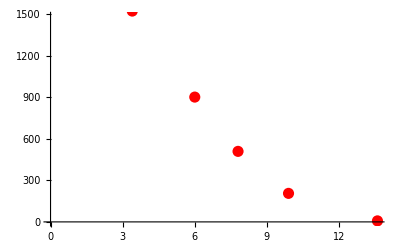

```mathematica
Show[{ErrorListPlot[Ncollmean,PlotStyle->{PointSize[0.02]}],ListPlot[Ncollbar,PlotStyle->{Red,PointSize[0.02]}]}]
```

The inelastic cross section:

```mathematica
dσABdb[b_,σi_]:=(1-(1-0.1*TAB[b,0]*σi)^(208*208))
```

Total inelastic nucleus - nucleus cross section in barn:

```mathematica
σAB[σi_?NumericQ]:=0.02 π NIntegrate[ dσABdb[b,σi]b,{b,0,40},Method->"AdaptiveMonteCarlo"]
```

```mathematica
σAB[64.0]
```

$Aborted

```mathematica
Npart[bx_?NumericQ,by_?NumericQ,σi_?NumericQ]:=2*208*NIntegrate[ρws[sx-bx,sy-by,zA]*(1-(1-0.1*Tws[sx,sy]*σi)^208),{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},Method->"AdaptiveMonteCarlo"]
```

Let us naively compare to Table II with b = b mean and  σ_inel^NN=64 mb in arXiv : 1102.1957:

```mathematica
Nparbar={{3.4,Npart[3.4,0,64.]},{6.0,Npart[6.0,0,64.]},{7.8,Npart[7.8,0,64.]},{9.9,Npart[9.9,0,64.]},{13.6,Npart[13.6,0,64.]}};
Needs["ErrorBarPlots`"];Npartmean={{{3.4,355},ErrorBar[3]},{{6.0,261},ErrorBar[4]},{{7.8,187},ErrorBar[5]},{{9.9,108},ErrorBar[5]},{{13.6,22},ErrorBar[2]}};
```

```mathematica
Join[{{b mean, Npart Optic, Npart MC}},Transpose[{Nparbar[[All,1]],Nparbar[[All,2]],Npartmean[[All,1]][[All,2]]}]]//TableForm
```

b mean | Npart Optic | MC Npart
3.4 | 345.782 | 355
6. | 235.582 | 261
7.8 | 167.498 | 187
9.9 | 86.5436 | 108
13.6 | 8.00013 | 22

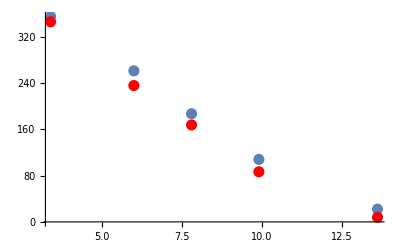

```mathematica
Show[{ErrorListPlot[Npartmean,PlotStyle->{PointSize[0.02]}],ListPlot[Nparbar,PlotStyle->{Red,PointSize[0.02]}]}]
```

## Centrality bins of PbPb (arXiv:1301.4361)

Let us define centrality bins according to the differential cross section in b according to arXiv : 1301.4361. The centrality percentile is defined as

### Centrality

```mathematica
cp[bmin_?NumericQ,bmax_?NumericQ,σi_?NumericQ]:=1/7.518980474346866 0.02 π NIntegrate[ dσABdb[b,σi]b,{b,bmin,bmax},Method->"MonteCarloRule"]
```

```mathematica
dσdb[b_,σi_]:=1/7.518980474346866 0.02*π*dσABdb[b,σi]b
```

```mathematica
dσdbls=Table[{b,dσdb[b,64.0]},{b,0,20,0.1}]
```

{{0.,0.},{0.1,0.000835643},{0.2,0.00167129},{0.3,0.00250693},{0.4,0.00334257},{0.5,0.00417822},{0.6,0.00501386},{0.7,0.0058495},{0.8,0.00668515},{0.9,0.00752079},{1.,0.00835643},{1.1,0.00919208},{1.2,0.0100277},{1.3,0.0108634},{1.4,0.011699},{1.5,0.0125346},{1.6,0.0133703},{1.7,0.0142059},{1.8,0.0150416},{1.9,0.0158772},{2.,0.0167129},{2.1,0.0175485},{2.2,0.0183842},{2.3,0.0192198},{2.4,0.0200554},{2.5,0.0208911},{2.6,0.0217267},{2.7,0.0225624},{2.8,0.023398},{2.9,0.0242337},{3.,0.0250693},{3.1,0.0259049},{3.2,0.0267406},{3.3,0.0275762},{3.4,0.0284119},{3.5,0.0292475},{3.6,0.0300832},{3.7,0.0309188},{3.8,0.0317544},{3.9,0.0325901},{4.,0.0334257},{4.1,0.0342614},{4.2,0.035097},{4.3,0.0359327},{4.4,0.0367683},{4.5,0.0376039},{4.6,0.0384396},{4.7,0.0392752},{4.8,0.0401109},{4.9,0.0409465},{5.,0.0417822},{5.1,0.0426178},{5.2,0.0434534},{5.3,0.0442891},{5.4,0.0451247},{5.5,0.0459604},{5.6,0.046796},{5.7,0.0476317},{5.8,0.0484673},{5.9,0.049303},{6.,0.0501386},{6.1,0.0509742},{6.2,0.0518099},{6.3,0.0526455},{6.4,0.0534812},{6.5,0.0543168},{6.6,0.0551525},{6.7,0.0559881},{6.8,0.0568237},{6.9,0.0576594},{7.,0.058495},{7.1,0.0593307},{7.2,0.0601663},{7.3,0.061002},{7.4,0.0618376},{7.5,0.0626732},{7.6,0.0635089},{7.7,0.0643445},{7.8,0.0651802},{7.9,0.0660158},{8.,0.0668515},{8.1,0.0676871},{8.2,0.0685227},{8.3,0.0693584},{8.4,0.070194},{8.5,0.0710297},{8.6,0.0718653},{8.7,0.072701},{8.8,0.0735366},{8.9,0.0743722},{9.,0.0752079},{9.1,0.0760435},{9.2,0.0768792},{9.3,0.0777148},{9.4,0.0785505},{9.5,0.0793861},{9.6,0.0802218},{9.7,0.0810574},{9.8,0.081893},{9.9,0.0827287},{10.,0.0835643},{10.1,0.0844},{10.2,0.0852356},{10.3,0.0860713},{10.4,0.0869069},{10.5,0.0877425},{10.6,0.0885782},{10.7,0.0894138},{10.8,0.0902495},{10.9,0.0910851},{11.,0.0919208},{11.1,0.0927564},{11.2,0.093592},{11.3,0.0944277},{11.4,0.0952633},{11.5,0.096099},{11.6,0.0969346},{11.7,0.0977703},{11.8,0.0986059},{11.9,0.0994415},{12.,0.100277},{12.1,0.101113},{12.2,0.101948},{12.3,0.102784},{12.4,0.10362},{12.5,0.104455},{12.6,0.105291},{12.7,0.106127},{12.8,0.106962},{12.9,0.107798},{13.,0.108634},{13.1,0.109469},{13.2,0.110305},{13.3,0.111139},{13.4,0.111973},{13.5,0.1128},{13.6,0.113614},{13.7,0.114398},{13.8,0.11508},{13.9,0.115781},{14.,0.11611},{14.1,0.116206},{14.2,0.116074},{14.3,0.115184},{14.4,0.113698},{14.5,0.11127},{14.6,0.108507},{14.7,0.104443},{14.8,0.100094},{14.9,0.0951593},{15.,0.0891401},{15.1,0.0827249},{15.2,0.0762945},{15.3,0.0705519},{15.4,0.0647518},{15.5,0.0588913},{15.6,0.0530077},{15.7,0.0477685},{15.8,0.042009},{15.9,0.0377307},{16.,0.0329361},{16.1,0.0293857},{16.2,0.0258157},{16.3,0.0223794},{16.4,0.0198781},{16.5,0.0171623},{16.6,0.0147757},{16.7,0.0130059},{16.8,0.0113275},{16.9,0.00967474},{17.,0.00845849},{17.1,0.00726487},{17.2,0.00633267},{17.3,0.00534054},{17.4,0.00462359},{17.5,0.00397938},{17.6,0.00340103},{17.7,0.00289742},{17.8,0.00254038},{17.9,0.00215419},{18.,0.00185106},{18.1,0.00158163},{18.2,0.00134937},{18.3,0.00116277},{18.4,0.00100245},{18.5,0.000850258},{18.6,0.000728297},{18.7,0.000614111},{18.8,0.000534538},{18.9,0.000458345},{19.,0.000379983},{19.1,0.000338261},{19.2,0.000280507},{19.3,0.000239496},{19.4,0.00020356},{19.5,0.000175532},{19.6,0.000147892},{19.7,0.000126193},{19.8,0.000108976},{19.9,0.0000928814},{20.,0.0000797482}}

```mathematica
dσdbls={{0.,0.},{0.1,0.00083564325357892},{0.2,0.00167128650715784},{0.30000000000000004,0.0025069297607367602},{0.4,0.00334257301431568},{0.5,0.0041782162678946},{0.6000000000000001,0.0050138595214735205},{0.7000000000000001,0.00584950277505244},{0.8,0.00668514602863136},{0.9,0.007520789282210279},{1.,0.0083564325357892},{1.1,0.00919207578936812},{1.2000000000000002,0.010027719042947041},{1.3,0.01086336229652596},{1.4000000000000001,0.01169900555010488},{1.5,0.0125346488036838},{1.6,0.01337029205726272},{1.7000000000000002,0.01420593531084164},{1.8,0.015041578564420559},{1.9000000000000001,0.01587722181799948},{2.,0.0167128650715784},{2.1,0.01754850832515732},{2.2,0.01838415157873624},{2.3000000000000003,0.019219794832315163},{2.4000000000000004,0.020055438085894082},{2.5,0.020891081339472997},{2.6,0.02172672459305192},{2.7,0.02256236784663084},{2.8000000000000003,0.02339801110020976},{2.9000000000000004,0.024233654353788683},{3.,0.0250692976073676},{3.1,0.025904940860946517},{3.2,0.02674058411452544},{3.3000000000000003,0.02757622736810436},{3.4000000000000004,0.02841187062168328},{3.5,0.029247513875262195},{3.6,0.030083157128841118},{3.7,0.030918800382420043},{3.8000000000000003,0.03175444363599896},{3.9000000000000004,0.03259008688957788},{4.,0.0334257301431568},{4.1000000000000005,0.03426137339673572},{4.2,0.03509701665031464},{4.3,0.035932659903893556},{4.4,0.03676830315747248},{4.5,0.0376039464110514},{4.6000000000000005,0.038439589664630326},{4.7,0.03927523291820924},{4.800000000000001,0.040110876171788164},{4.9,0.04094651942536708},{5.,0.041782162678945994},{5.1000000000000005,0.04261780593252493},{5.2,0.04345344918610384},{5.300000000000001,0.044289092439682765},{5.4,0.04512473569326168},{5.5,0.0459603789468406},{5.6000000000000005,0.04679602220041952},{5.7,0.04763166545399844},{5.800000000000001,0.048467308707577365},{5.9,0.049302951961156284},{6.,0.0501385952147352},{6.1000000000000005,0.050974238468314115},{6.2,0.051809881721893034},{6.300000000000001,0.052645524975471966},{6.4,0.05348116822905088},{6.5,0.0543168114826298},{6.6000000000000005,0.05515245473620872},{6.7,0.05598809798978764},{6.800000000000001,0.05682374124336656},{6.9,0.05765938449694548},{7.,0.05849502775052439},{7.1000000000000005,0.05933067100410332},{7.2,0.060166314257682235},{7.300000000000001,0.06100195751126117},{7.4,0.06183760076484009},{7.5,0.062673244018419},{7.6000000000000005,0.06350888727199792},{7.7,0.06434453052557683},{7.800000000000001,0.06518017377915576},{7.9,0.06601581703273468},{8.,0.0668514602863136},{8.1,0.06768710353989252},{8.200000000000001,0.06852274679347144},{8.3,0.06935839004705036},{8.4,0.07019403330062927},{8.5,0.0710296765542082},{8.6,0.07186531980778711},{8.700000000000001,0.07270096306136604},{8.8,0.07353660631494496},{8.9,0.07437224956852388},{9.,0.0752078928221028},{9.1,0.07604353607568172},{9.200000000000001,0.07687917932926065},{9.3,0.07771482258283956},{9.4,0.07855046583641848},{9.5,0.0793861090899974},{9.600000000000001,0.08022175234357633},{9.700000000000001,0.08105739559715525},{9.8,0.08189303885073417},{9.9,0.08272868210431307},{10.,0.08356432535789199},{10.100000000000001,0.08439996861147094},{10.200000000000001,0.08523561186504985},{10.3,0.08607125511862877},{10.4,0.08690689837220768},{10.5,0.0877425416257866},{10.600000000000001,0.08857818487936553},{10.700000000000001,0.08941382813294445},{10.8,0.09024947138652337},{10.9,0.09108511464010229},{11.,0.0919207578936812},{11.100000000000001,0.09275640114726012},{11.200000000000001,0.09359204440083904},{11.3,0.09442768765441796},{11.4,0.09526333090799688},{11.5,0.0960989741615758},{11.600000000000001,0.09693461741515473},{11.700000000000001,0.09777026066873365},{11.8,0.09860590392231257},{11.9,0.09944154717589147},{12.,0.1002771904294704},{12.100000000000001,0.10111283368304932},{12.200000000000001,0.10194847693662823},{12.3,0.10278412019020708},{12.4,0.10361976344378435},{12.5,0.10445540669731662},{12.600000000000001,0.10529104995016517},{12.700000000000001,0.10612669319291364},{12.8,0.10696233632904491},{12.9,0.10779797820135933},{13.,0.10863361647693988},{13.100000000000001,0.10946923013124081},{13.200000000000001,0.1103047203070988},{13.3,0.11113947714580814},{13.4,0.11197307457294081},{13.5,0.1128000334781842},{13.600000000000001,0.1136140524745288},{13.700000000000001,0.1143980705547839},{13.8,0.11508037882611806},{13.9,0.11578106316341999},{14.,0.11610958151090194},{14.100000000000001,0.11620592671186099},{14.200000000000001,0.11607362674325776},{14.3,0.11518379544874408},{14.4,0.11369819499845721},{14.5,0.11126981636095619},{14.600000000000001,0.10850676058273698},{14.700000000000001,0.10444321967124853},{14.8,0.100093567516516},{14.9,0.09515931323438107},{15.,0.08914010931587957},{15.100000000000001,0.08272487728410563},{15.200000000000001,0.07629449860170648},{15.3,0.07055189642585925},{15.4,0.06475181227916244},{15.5,0.05889125071640839},{15.600000000000001,0.05300768523905745},{15.700000000000001,0.04776852898984907},{15.8,0.04200903372468749},{15.9,0.0377307176658664},{16.,0.032936053885053496},{16.1,0.029385731202596656},{16.2,0.025815719034137093},{16.3,0.022379391415824217},{16.400000000000002,0.01987809522928505},{16.5,0.017162281303148154},{16.6,0.014775666541172836},{16.7,0.01300586755759551},{16.8,0.011327489734050802},{16.900000000000002,0.009674737325566696},{17.,0.008458492942303712},{17.1,0.007264866328534938},{17.2,0.006332674085032497},{17.3,0.005340542597930236},{17.400000000000002,0.004623585596678837},{17.5,0.003979377359171736},{17.6,0.0034010282930590423},{17.7,0.0028974202563024198},{17.8,0.0025403800847024084},{17.900000000000002,0.002154192447225687},{18.,0.0018510581665496886},{18.1,0.001581627355222872},{18.2,0.001349368140897183},{18.3,0.0011627730280805155},{18.400000000000002,0.0010024484696340207},{18.5,0.0008502581318741103},{18.6,0.0007282966996586448},{18.7,0.0006141113219235383},{18.8,0.0005345384077434045},{18.900000000000002,0.0004583450289127757},{19.,0.00037998285107093064},{19.1,0.00033826081108743545},{19.200000000000003,0.0002805074014917288},{19.3,0.00023949575670434932},{19.400000000000002,0.00020355987629821338},{19.5,0.00017553214450262295},{19.6,0.0001478919425439414},{19.700000000000003,0.00012619330406961327},{19.8,0.00010897603375315203},{19.900000000000002,0.00009288139314920188},{20.,0.0000797482288004821}};
```

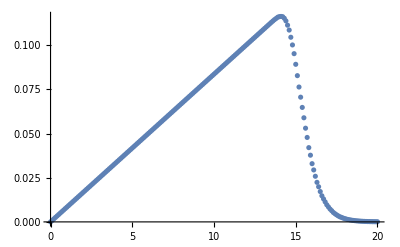

```mathematica
ListPlot[dσdbls]
```

Compare to MC Glauber :

```mathematica
Import["impactpar.pdf"]
```

{-Graphics-}

The optical Glauber has a sharper edge.

So it does not do the trick.

```mathematica
dσdbInterp=Interpolation[dσdbls,InterpolationOrder->1]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
NIntegrate[dσdbInterp[b],{b,0,20}]
```

1.01053

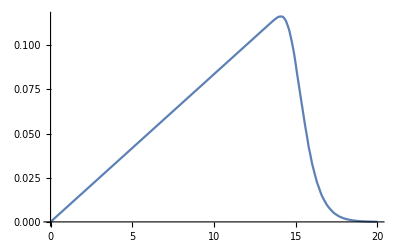

```mathematica
Plot[dσdbInterp[b],{b,0,20}]
```

```mathematica
cpInterp[b_]:= NIntegrate[dσdbInterp[bi] ,{bi,0,b}]
```

```mathematica
cpls=Table[{b,cpInterp[b]},{b,0,20,0.1}]
```

{{0.,0},{0.1,0.0000417822},{0.2,0.000167129},{0.3,0.000376039},{0.4,0.000668515},{0.5,0.00104455},{0.6,0.00150416},{0.7,0.00204733},{0.8,0.00267406},{0.9,0.00338436},{1.,0.00417822},{1.1,0.00505564},{1.2,0.00601663},{1.3,0.00706119},{1.4,0.0081893},{1.5,0.00940099},{1.6,0.0106962},{1.7,0.012075},{1.8,0.0135374},{1.9,0.0150834},{2.,0.0167129},{2.1,0.0184259},{2.2,0.0202226},{2.3,0.0221028},{2.4,0.0240665},{2.5,0.0261139},{2.6,0.0282447},{2.7,0.0304592},{2.8,0.0327572},{2.9,0.0351388},{3.,0.0376039},{3.1,0.0401527},{3.2,0.0427849},{3.3,0.0455008},{3.4,0.0483002},{3.5,0.0511831},{3.6,0.0541497},{3.7,0.0571998},{3.8,0.0603334},{3.9,0.0635507},{4.,0.0668515},{4.1,0.0702358},{4.2,0.0737037},{4.3,0.0772552},{4.4,0.0808903},{4.5,0.0846089},{4.6,0.0884111},{4.7,0.0922968},{4.8,0.0962661},{4.9,0.100319},{5.,0.104455},{5.1,0.108675},{5.2,0.112979},{5.3,0.117366},{5.4,0.121837},{5.5,0.126391},{5.6,0.131029},{5.7,0.13575},{5.8,0.140555},{5.9,0.145444},{6.,0.150416},{6.1,0.155471},{6.2,0.160611},{6.3,0.165833},{6.4,0.17114},{6.5,0.17653},{6.6,0.182003},{6.7,0.18756},{6.8,0.193201},{6.9,0.198925},{7.,0.204733},{7.1,0.210624},{7.2,0.216599},{7.3,0.222657},{7.4,0.228799},{7.5,0.235025},{7.6,0.241334},{7.7,0.247726},{7.8,0.254203},{7.9,0.260762},{8.,0.267406},{8.1,0.274133},{8.2,0.280943},{8.3,0.287837},{8.4,0.294815},{8.5,0.301876},{8.6,0.309021},{8.7,0.316249},{8.8,0.323561},{8.9,0.330957},{9.,0.338436},{9.1,0.345998},{9.2,0.353644},{9.3,0.361374},{9.4,0.369187},{9.5,0.377084},{9.6,0.385064},{9.7,0.393128},{9.8,0.401276},{9.9,0.409507},{10.,0.417822},{10.1,0.42622},{10.2,0.434702},{10.3,0.443267},{10.4,0.451916},{10.5,0.460648},{10.6,0.469464},{10.7,0.478364},{10.8,0.487347},{10.9,0.496414},{11.,0.505564},{11.1,0.514798},{11.2,0.524115},{11.3,0.533516},{11.4,0.543001},{11.5,0.552569},{11.6,0.562221},{11.7,0.571956},{11.8,0.581775},{11.9,0.591677},{12.,0.601663},{12.1,0.611733},{12.2,0.621886},{12.3,0.632122},{12.4,0.642443},{12.5,0.652846},{12.6,0.663334},{12.7,0.673905},{12.8,0.684559},{12.9,0.695297},{13.,0.706119},{13.1,0.717024},{13.2,0.728012},{13.3,0.739085},{13.4,0.75024},{13.5,0.761479},{13.6,0.7728},{13.7,0.7842},{13.8,0.795674},{13.9,0.807217},{14.,0.818812},{14.1,0.830427},{14.2,0.842041},{14.3,0.853604},{14.4,0.865048},{14.5,0.876297},{14.6,0.887286},{14.7,0.897933},{14.8,0.90816},{14.9,0.917923},{15.,0.927138},{15.1,0.935731},{15.2,0.943682},{15.3,0.951024},{15.4,0.957789},{15.5,0.963972},{15.6,0.969566},{15.7,0.974605},{15.8,0.979094},{15.9,0.983081},{16.,0.986614},{16.1,0.989731},{16.2,0.992491},{16.3,0.9949},{16.4,0.997013},{16.5,0.998865},{16.6,1.00046},{16.7,1.00185},{16.8,1.00307},{16.9,1.00412},{17.,1.00502},{17.1,1.00581},{17.2,1.00649},{17.3,1.00707},{17.4,1.00757},{17.5,1.008},{17.6,1.00837},{17.7,1.00869},{17.8,1.00896},{17.9,1.00919},{18.,1.00939},{18.1,1.00957},{18.2,1.00971},{18.3,1.00984},{18.4,1.00995},{18.5,1.01004},{18.6,1.01012},{18.7,1.01018},{18.8,1.01024},{18.9,1.01029},{19.,1.01033},{19.1,1.01037},{19.2,1.0104},{19.3,1.01043},{19.4,1.01045},{19.5,1.01047},{19.6,1.01048},{19.7,1.0105},{19.8,1.01051},{19.9,1.01052},{20.,1.01053}}

```mathematica
cInterp=Interpolation[cpls]
```

InterpolatingFunction[{{0., 20.}}, <>]

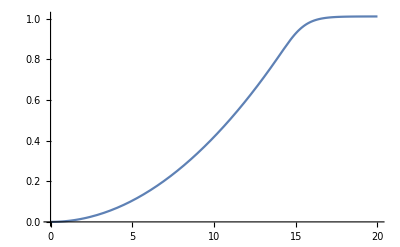

```mathematica
Plot[cInterp[b],{b,0,20}]
```

### b for centrality bins

Refined b list :

```mathematica
bls=Table[{cbin,c/.FindRoot[cInterp[c]==cbin,{c,1.0}]},{cbin,0.01,0.05,0.01}]
```

{{0.01,1.54705},{0.02,2.18786},{0.03,2.67957},{0.04,3.0941},{0.05,3.45931}}

```mathematica
bls=Join[bls,Table[{cbin,c/.FindRoot[cInterp[c]==cbin,{c,10*cbin}]},{cbin,0.1,0.95,0.05}]]
```

{{0.01,1.54705},{0.02,2.18786},{0.03,2.67957},{0.04,3.0941},{0.05,3.45931},{0.1,4.8922},{0.15,5.9917},{0.2,6.91862},{0.25,7.73525},{0.3,8.47355},{0.35,9.15248},{0.4,9.78441},{0.45,10.3779},{0.5,10.9393},{0.55,11.4732},{0.6,11.9834},{0.65,12.4727},{0.7,12.9436},{0.75,13.3979},{0.8,13.8377},{0.85,14.2701},{0.9,14.7299},{0.95,15.3213}}

```mathematica
bls=Join[{{0,0}},bls,{{1.0,20}}]
```

{{0,0},{0.01,1.54705},{0.02,2.18786},{0.03,2.67957},{0.04,3.0941},{0.05,3.45931},{0.1,4.8922},{0.15,5.9917},{0.2,6.91862},{0.25,7.73525},{0.3,8.47355},{0.35,9.15248},{0.4,9.78441},{0.45,10.3779},{0.5,10.9393},{0.55,11.4732},{0.6,11.9834},{0.65,12.4727},{0.7,12.9436},{0.75,13.3979},{0.8,13.8377},{0.85,14.2701},{0.9,14.7299},{0.95,15.3213},{1.,20}}

Coarse b list :

```mathematica
cls={0.05,0.1,0.2,0.4,0.6,0.8};
bcls=Table[{cls[[i]],c/.FindRoot[cInterp[c]==cls[[i]],{c,10*cls[[i]]}]},{i,1,Length[cls]}]
```

{{0.05,3.45931},{0.1,4.8922},{0.2,6.91862},{0.4,9.78441},{0.6,11.9834},{0.8,13.8377}}

```mathematica
bcls=Join[{{0,0}},bcls,{{1.0,20}}]
```

{{0,0},{0.05,3.45931},{0.1,4.8922},{0.2,6.91862},{0.4,9.78441},{0.6,11.9834},{0.8,13.8377},{1.,20}}

They agree with Table I very well.

```mathematica
cls={0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85};
bcls=Table[{cls[[i]],c/.FindRoot[cInterp[c]==cls[[i]],{c,10*cls[[i]]}]},{i,1,Length[cls]}]
```

{{0.05,3.45931},{0.15,5.9917},{0.25,7.73525},{0.35,9.15248},{0.45,10.3779},{0.55,11.4732},{0.65,12.4727},{0.75,13.3979},{0.85,14.2704}}

```mathematica
bcls=Join[{{0,0}},bcls,{{1.0,20}}]
```

{{0,0},{0.05,3.45931},{0.15,5.9917},{0.25,7.73525},{0.35,9.15248},{0.45,10.3779},{0.55,11.4732},{0.65,12.4727},{0.75,13.3979},{0.85,14.2704},{1.,20}}

### Ncoll

```mathematica
Ncollls=Table[{b,Ncoll[b,0,64.0]},{b,0,20,0.1}]
```

{{0.,1962.7},{0.1,1968.34},{0.2,1934.27},{0.3,2006.02},{0.4,1979.12},{0.5,1969.15},{0.6,1953.24},{0.7,1923.28},{0.8,1948.97},{0.9,1951.85},{1.,1913.06},{1.1,1911.23},{1.2,1913.05},{1.3,1924.61},{1.4,1910.95},{1.5,1852.28},{1.6,1891.04},{1.7,1809.46},{1.8,1828.04},{1.9,1828.31},{2.,1797.87},{2.1,1756.65},{2.2,1780.85},{2.3,1753.98},{2.4,1710.77},{2.5,1718.64},{2.6,1706.52},{2.7,1661.81},{2.8,1626.89},{2.9,1647.73},{3.,1608.83},{3.1,1591.54},{3.2,1569.91},{3.3,1554.25},{3.4,1514.63},{3.5,1503.03},{3.6,1516.18},{3.7,1465.8},{3.8,1418.73},{3.9,1406.37},{4.,1399.07},{4.1,1376.76},{4.2,1343.03},{4.3,1300.39},{4.4,1283.95},{4.5,1269.07},{4.6,1256.35},{4.7,1220.4},{4.8,1185.95},{4.9,1188.79},{5.,1173.93},{5.1,1111.38},{5.2,1107.96},{5.3,1049.66},{5.4,1055.94},{5.5,1042.17},{5.6,990.338},{5.7,976.963},{5.8,951.001},{5.9,930.244},{6.,901.715},{6.1,891.785},{6.2,859.718},{6.3,855.35},{6.4,824.698},{6.5,796.578},{6.6,767.395},{6.7,759.946},{6.8,736.42},{6.9,709.01},{7.,702.453},{7.1,668.629},{7.2,651.059},{7.3,623.22},{7.4,605.751},{7.5,580.752},{7.6,562.569},{7.7,535.362},{7.8,533.646},{7.9,521.279},{8.,465.755},{8.1,470.623},{8.2,466.758},{8.3,420.861},{8.4,422.989},{8.5,394.632},{8.6,391.001},{8.7,373.232},{8.8,345.013},{8.9,342.086},{9.,317.602},{9.1,305.229},{9.2,298.802},{9.3,285.233},{9.4,267.042},{9.5,249.137},{9.6,232.53},{9.7,231.225},{9.8,216.092},{9.9,205.762},{10.,196.163},{10.1,183.513},{10.2,167.832},{10.3,161.139},{10.4,152.994},{10.5,142.133},{10.6,131.983},{10.7,122.796},{10.8,109.718},{10.9,109.194},{11.,100.976},{11.1,95.3527},{11.2,85.6722},{11.3,83.3262},{11.4,72.6844},{11.5,68.7552},{11.6,60.1547},{11.7,55.7323},{11.8,52.9566},{11.9,49.3379},{12.,43.2729},{12.1,40.7567},{12.2,37.657},{12.3,33.1034},{12.4,30.2053},{12.5,26.5839},{12.6,23.703},{12.7,22.4139},{12.8,19.6667},{12.9,17.9835},{13.,16.1223},{13.1,14.1228},{13.2,12.4634},{13.3,10.8786},{13.4,9.90276},{13.5,8.78046},{13.6,7.87581},{13.7,6.87464},{13.8,6.22264},{13.9,5.4518},{14.,4.77761},{14.1,4.00633},{14.2,3.57711},{14.3,3.2037},{14.4,2.70491},{14.5,2.37381},{14.6,2.0813},{14.7,1.84932},{14.8,1.61614},{14.9,1.35992},{15.,1.20037},{15.1,1.04911},{15.2,0.925313},{15.3,0.795741},{15.4,0.685428},{15.5,0.593978},{15.6,0.489215},{15.7,0.424508},{15.8,0.377782},{15.9,0.308793},{16.,0.26586},{16.1,0.236656},{16.2,0.194661},{16.3,0.179545},{16.4,0.151525},{16.5,0.129289},{16.6,0.110369},{16.7,0.0940145},{16.8,0.0772156},{16.9,0.0667921},{17.,0.0579123},{17.1,0.0502717},{17.2,0.0430829},{17.3,0.0358379},{17.4,0.0316263},{17.5,0.0269291},{17.6,0.0225364},{17.7,0.0191604},{17.8,0.0158429},{17.9,0.0142524},{18.,0.0118096},{18.1,0.0103238},{18.2,0.00829277},{18.3,0.00748151},{18.4,0.00619642},{18.5,0.00529819},{18.6,0.00450355},{18.7,0.00386643},{18.8,0.00332249},{18.9,0.00281758},{19.,0.00239798},{19.1,0.00201011},{19.2,0.00167112},{19.3,0.00147776},{19.4,0.00120152},{19.5,0.00102855},{19.6,0.000878848},{19.7,0.00074134},{19.8,0.000628626},{19.9,0.000544028},{20.,0.000455329}}

```mathematica
NcollInterp= Interpolation[Ncollls,InterpolationOrder->1]
```

InterpolatingFunction[{{0., 20.}}, <>]

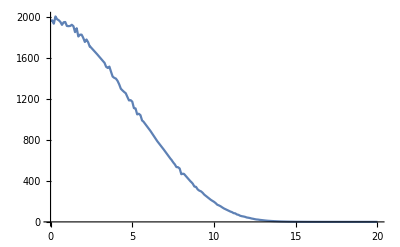

```mathematica
Plot[NcollInterp[b],{b,0,20}]
```

```mathematica
Ncollls=Table[{bcls[[i,1]],bcls[[i+1,1]],NIntegrate[NcollInterp[b]*dσdbInterp[b],{b,bcls[[i,2]],bcls[[i+1,2]]}]/(bcls[[i+1,1]]-bcls[[i,1]])},{i,1,Length[bcls]-1}]
```

{{0,0.05,1728.02},{0.05,0.1,1337.44},{0.1,0.2,922.015},{0.2,0.4,424.233},{0.4,0.6,113.701},{0.6,0.8,19.6857},{0.8,1.,2.14794}}

#### Check the dependence of the number of data point

```mathematica
Ncollls=Table[{b,Ncoll[b,0,64.0]},{b,0,20,0.2}]
```

{{0.,1958.33},{0.2,2011.89},{0.4,1959.08},{0.6,1960.39},{0.8,1947.83},{1.,1922.05},{1.2,1899.64},{1.4,1913.1},{1.6,1863.75},{1.8,1817.18},{2.,1799.57},{2.2,1734.3},{2.4,1742.65},{2.6,1676.},{2.8,1615.18},{3.,1607.83},{3.2,1587.71},{3.4,1502.4},{3.6,1463.88},{3.8,1433.02},{4.,1378.95},{4.2,1324.12},{4.4,1284.04},{4.6,1241.93},{4.8,1187.26},{5.,1155.88},{5.2,1088.92},{5.4,1056.99},{5.6,979.113},{5.8,965.657},{6.,898.165},{6.2,843.616},{6.4,823.488},{6.6,778.458},{6.8,731.19},{7.,693.822},{7.2,651.546},{7.4,611.138},{7.6,571.901},{7.8,533.206},{8.,475.98},{8.2,445.623},{8.4,410.272},{8.6,390.849},{8.8,347.381},{9.,323.944},{9.2,298.247},{9.4,266.894},{9.6,237.569},{9.8,213.227},{10.,193.764},{10.2,173.402},{10.4,149.299},{10.6,130.673},{10.8,116.704},{11.,100.915},{11.2,86.8088},{11.4,75.384},{11.6,62.8444},{11.8,52.0452},{12.,43.7614},{12.2,35.0908},{12.4,29.3605},{12.6,25.3214},{12.8,19.8534},{13.,15.9389},{13.2,12.1418},{13.4,10.2414},{13.6,7.86516},{13.8,5.99047},{14.,4.45811},{14.2,3.63681},{14.4,2.80224},{14.6,2.03873},{14.8,1.60618},{15.,1.18881},{15.2,0.905661},{15.4,0.658011},{15.6,0.502342},{15.8,0.366439},{16.,0.277414},{16.2,0.208079},{16.4,0.147746},{16.6,0.111412},{16.8,0.0840333},{17.,0.0555873},{17.2,0.0429202},{17.4,0.0314796},{17.6,0.0219975},{17.8,0.0166357},{18.,0.0118978},{18.2,0.00860372},{18.4,0.0063577},{18.6,0.00460534},{18.8,0.00329538},{19.,0.00241473},{19.2,0.00172235},{19.4,0.00121359},{19.6,0.000858908},{19.8,0.0006345},{20.,0.000446826}}

```mathematica
NcollInterp= Interpolation[Ncollls,InterpolationOrder->2]
```

InterpolatingFunction[{{0., 20.}}, <>]

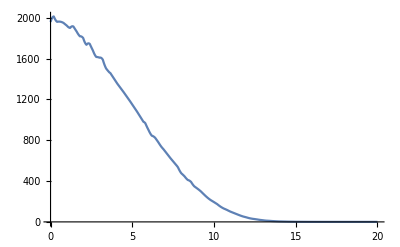

```mathematica
Plot[NcollInterp[b],{b,0,20}]
```

```mathematica
Ncollls=Table[{bcls[[i,1]],bcls[[i+1,1]],NIntegrate[NcollInterp[b]*dσdbInterp[b],{b,bcls[[i,2]],bcls[[i+1,2]]}]/(bcls[[i+1,1]]-bcls[[i,1]])},{i,1,Length[bcls]-1}]
```

{{0,0.05,1722.37},{0.05,0.1,1326.55},{0.1,0.2,917.556},{0.2,0.4,424.429},{0.4,0.6,113.748},{0.6,0.8,19.5002},{0.8,1.,2.11273}}

### Npart

Glauber MC gives in Table I:

```mathematica
NpartMC={{0,0.05,382.7},{0.05,0.1,329.4},{0.1,0.2,260.1},{0.2,0.4,157.2},{0.4,0.6,68.56},{0.6,0.8,22.52},{0.8,1.,5.604}};
```

```mathematica
Npartc[bmin_?NumericQ,bmax_?NumericQ,σi_?NumericQ]:=2*208*NIntegrate[dσdbInterp[b]*ρws[sx-b,sy,zA]*(1-(1-0.1*TwsInterp[Sqrt[sx*sx+sy*sy]]*σi)^208),{b,bmin,bmax},{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},Method->"AdaptiveMonteCarlo"]
```

Glauber Model gives

```mathematica
Npartcls=Table[{bcls[[i,1]],bcls[[i+1,1]],Npartc[bcls[[i,2]],bcls[[i+1,2]],64.0]/(bcls[[i+1,1]]-bcls[[i,1]])},{i,1,Length[bcls]-1}]
```

{{0,0.05,364.84},{0.05,0.1,318.365},{0.1,0.2,238.606},{0.2,0.4,136.742},{0.4,0.6,51.1511},{0.6,0.8,15.9337},{0.8,1.,2.59931}}

The relative error:

```mathematica
NpartMC[[All,3]]/Npartcls[[All,3]]-1.0
```

{0.0489538,0.0346619,0.09008,0.149612,0.340343,0.413353,1.15596}

Refined centrality bins :

```mathematica
NpartrMC={{0,0.01,403.8},{0.01,0.02,393.6},{0.02,0.03,382.9},{0.03,0.04,372.0},{0.04,0.05,361.1},{0.05,0.1,329.4},{0.1,0.15000000000000002,281.2},{0.15000000000000002,0.2,239.0},{0.2,0.25,202.1},{0.25,0.30000000000000004,169.5},{0.30000000000000004,0.35,141.0},{0.35,0.4,116.0},{0.4,0.45000000000000007,94.11},{0.45000000000000007,0.5,75.3},{0.5,0.55,59.24},{0.55,0.6,45.58},{0.6,0.65,34.33},{0.65,0.7000000000000001,25.21},{0.7000000000000001,0.75,17.96},{0.75,0.8,12.58},{0.8,0.85,8.812},{0.85,0.9,6.158},{0.9,0.9500000000000001,4.376},{0.9500000000000001,1.,3.064}};
```

```mathematica
Npartls=Table[{bls[[i,1]],bls[[i+1,1]],Npartc[bls[[i,2]],bls[[i+1,2]],64.0]/(bls[[i+1,1]]-bls[[i,1]])},{i,1,Length[bls]-1}]
```

{{0,0.01,390.27},{0.01,0.02,379.22},{0.02,0.03,370.338},{0.03,0.04,351.528},{0.04,0.05,345.729},{0.05,0.1,310.263},{0.1,0.15,262.561},{0.15,0.2,219.67},{0.2,0.25,174.583},{0.25,0.3,146.437},{0.3,0.35,121.924},{0.35,0.4,97.338},{0.4,0.45,81.3181},{0.45,0.5,58.7203},{0.5,0.55,47.5731},{0.55,0.6,34.6374},{0.6,0.65,25.4616},{0.65,0.7,16.872},{0.7,0.75,10.5066},{0.75,0.8,7.48367},{0.8,0.85,4.99233},{0.85,0.9,2.91131},{0.9,0.95,1.598},{0.95,1.,0.576925}}

```mathematica
NpartrMC[[All,3]]/Npartls[[All,3]]-1.0
```

{0.0346676,0.0379195,0.0339208,0.0582361,0.044461,0.0616808,0.0709878,0.0879945,0.157612,0.157492,0.156461,0.191724,0.157307,0.282349,0.245242,0.31592,0.348303,0.494189,0.709406,0.680994,0.765106,1.1152,1.73843,4.31092}

```mathematica
Npartls=Table[{bcls[[i,1]],bcls[[i+1,1]],Npartc[bcls[[i,2]],bcls[[i+1,2]],64.0]/(bcls[[i+1,1]]-bcls[[i,1]])},{i,1,Length[bcls]-1}]
```

{{0,0.05,373.21},{0.05,0.15,288.273},{0.15,0.25,198.379},{0.25,0.35,133.406},{0.35,0.45,84.6128},{0.45,0.55,51.0637},{0.55,0.65,28.4132},{0.65,0.75,14.7089},{0.75,0.85,5.90986},{0.85,1.,1.73004}}

```mathematica
NpartlsUrs={{0,0.05,377},{0.05,0.15,302},{0.15,0.25,222},{0.25,0.35,160},{0.35,0.45,112},{0.45,0.55,75},{0.55,0.65,47},{0.65,0.75,27},{0.75,0.85,14},{0.85,1.,1.7300425306302267}}
```

{{0,0.05,377},{0.05,0.15,302},{0.15,0.25,222},{0.25,0.35,160},{0.35,0.45,112},{0.45,0.55,75},{0.55,0.65,47},{0.65,0.75,27},{0.75,0.85,14},{0.85,1.,1.73004}}

```mathematica
Transpose[{Npartls[[1;;-2,1]],Npartls[[1;;-2,2]],Npartls[[1;;-2,3]],NpartlsUrs[[1;;-2,3]],NpartlsUrs[[1;;-2,3]]/Npartls[[1;;-2,3]]-1.0}]//TableForm
```

0 | 0.05 | 373.21 | 377 | 0.0101564
0.05 | 0.15 | 288.273 | 302 | 0.0476163
0.15 | 0.25 | 198.379 | 222 | 0.11907
0.25 | 0.35 | 133.406 | 160 | 0.199346
0.35 | 0.45 | 84.6128 | 112 | 0.323677
0.45 | 0.55 | 51.0637 | 75 | 0.468753
0.55 | 0.65 | 28.4132 | 47 | 0.654162
0.65 | 0.75 | 14.7089 | 27 | 0.835621
0.75 | 0.85 | 5.90986 | 14 | 1.36892

## Flow

We take the initial energy density to be proportional to ρws[x,y-b/2] ρws[x,y+b/2].

Recall that the Thickness function in 1/fm^2 :

```mathematica
TAB[b_?NumericQ]:=NIntegrate[ρws[sx,sy-b/2,zA]*ρws[sx,sy+b/2,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo"(*,Method->{"MonteCarloRule","Points"->10^4}*)}]
```

```mathematica
Rrms[b_?NumericQ]:=Sqrt[1/TAB[b] NIntegrate[(sx^2+sy^2)ρws[sx,sy-b/2,zA]*ρws[sx,sy+b/2,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo"(*,Method->{"MonteCarloRule","Points"->10^6}*)}]]
```

```mathematica
δ2[b_?NumericQ]:=NIntegrate[(sx^2-sy^2)ρws[sx,sy-b/2,zA]*ρws[sx,sy+b/2,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->10^6}}]/NIntegrate[(sx^2+sy^2)ρws[sx,sy-b/2,zA]*ρws[sx,sy+b/2,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo"(*,Method->{"MonteCarloRule","Points"->10^6}*)}]
```

```mathematica
cls=Table[0.005*n,{n,0,180}]
```

{0.,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105,0.11,0.115,0.12,0.125,0.13,0.135,0.14,0.145,0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6,0.605,0.61,0.615,0.62,0.625,0.63,0.635,0.64,0.645,0.65,0.655,0.66,0.665,0.67,0.675,0.68,0.685,0.69,0.695,0.7,0.705,0.71,0.715,0.72,0.725,0.73,0.735,0.74,0.745,0.75,0.755,0.76,0.765,0.77,0.775,0.78,0.785,0.79,0.795,0.8,0.805,0.81,0.815,0.82,0.825,0.83,0.835,0.84,0.845,0.85,0.855,0.86,0.865,0.87,0.875,0.88,0.885,0.89,0.895,0.9}

```mathematica
(* cls={0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.52,0.54,0.56,0.58,0.60,0.64,0.655,0.685,0.715,0.735,0.765,0.79,0.815,0.845,0.9,0.94,0.98};*)
bcls=Table[{cls[[i]],c/.FindRoot[cInterp[c]==cls[[i]],{c,10*cls[[i]]}]},{i,1,Length[cls]}]
```

{{0.,0.},{0.005,1.09393},{0.01,1.54705},{0.015,1.89474},{0.02,2.18786},{0.025,2.4461},{0.03,2.67957},{0.035,2.89427},{0.04,3.0941},{0.045,3.28179},{0.05,3.45931},{0.055,3.62816},{0.06,3.78948},{0.065,3.94422},{0.07,4.09311},{0.075,4.23677},{0.08,4.37572},{0.085,4.51039},{0.09,4.64115},{0.095,4.76833},{0.1,4.8922},{0.105,5.01302},{0.11,5.13099},{0.115,5.2463},{0.12,5.35914},{0.125,5.46965},{0.13,5.57797},{0.135,5.68423},{0.14,5.78853},{0.145,5.89099},{0.15,5.9917},{0.155,6.09074},{0.16,6.1882},{0.165,6.28415},{0.17,6.37865},{0.175,6.47178},{0.18,6.56358},{0.185,6.65412},{0.19,6.74344},{0.195,6.83159},{0.2,6.91862},{0.205,7.00457},{0.21,7.08948},{0.215,7.17338},{0.22,7.25631},{0.225,7.33831},{0.23,7.41939},{0.235,7.49961},{0.24,7.57897},{0.245,7.65751},{0.25,7.73525},{0.255,7.81222},{0.26,7.88844},{0.265,7.96393},{0.27,8.03871},{0.275,8.1128},{0.28,8.18622},{0.285,8.25899},{0.29,8.33112},{0.295,8.40264},{0.3,8.47355},{0.305,8.54387},{0.31,8.61361},{0.315,8.6828},{0.32,8.75144},{0.325,8.81955},{0.33,8.88713},{0.335,8.9542},{0.34,9.02078},{0.345,9.08687},{0.35,9.15248},{0.355,9.21762},{0.36,9.2823},{0.365,9.34654},{0.37,9.41034},{0.375,9.47371},{0.38,9.53666},{0.385,9.5992},{0.39,9.66133},{0.395,9.72306},{0.4,9.78441},{0.405,9.84537},{0.41,9.90596},{0.415,9.96618},{0.42,10.026},{0.425,10.0855},{0.43,10.1447},{0.435,10.2035},{0.44,10.262},{0.445,10.3201},{0.45,10.3779},{0.455,10.4354},{0.46,10.4926},{0.465,10.5495},{0.47,10.606},{0.475,10.6623},{0.48,10.7183},{0.485,10.774},{0.49,10.8294},{0.495,10.8845},{0.5,10.9393},{0.505,10.9939},{0.51,11.0482},{0.515,11.1022},{0.52,11.1559},{0.525,11.2094},{0.53,11.2627},{0.535,11.3157},{0.54,11.3685},{0.545,11.421},{0.55,11.4732},{0.555,11.5253},{0.56,11.5771},{0.565,11.6286},{0.57,11.68},{0.575,11.7311},{0.58,11.782},{0.585,11.8327},{0.59,11.8831},{0.595,11.9334},{0.6,11.9834},{0.605,12.0332},{0.61,12.0829},{0.615,12.1323},{0.62,12.1815},{0.625,12.2305},{0.63,12.2793},{0.635,12.328},{0.64,12.3764},{0.645,12.4247},{0.65,12.4727},{0.655,12.5206},{0.66,12.5683},{0.665,12.6158},{0.67,12.6632},{0.675,12.7103},{0.68,12.7573},{0.685,12.8041},{0.69,12.8508},{0.695,12.8972},{0.7,12.9436},{0.705,12.9897},{0.71,13.0357},{0.715,13.0815},{0.72,13.1272},{0.725,13.1727},{0.73,13.218},{0.735,13.2632},{0.74,13.3082},{0.745,13.3531},{0.75,13.3979},{0.755,13.4424},{0.76,13.4869},{0.765,13.5312},{0.77,13.5753},{0.775,13.6194},{0.78,13.6632},{0.785,13.707},{0.79,13.7506},{0.795,13.7941},{0.8,13.8375},{0.805,13.8808},{0.81,13.924},{0.815,13.9672},{0.82,14.0102},{0.825,14.0533},{0.83,14.0963},{0.835,14.1393},{0.84,14.1824},{0.845,14.2255},{0.85,14.2687},{0.855,14.3121},{0.86,14.3557},{0.865,14.3996},{0.87,14.4438},{0.875,14.4884},{0.88,14.5334},{0.885,14.579},{0.89,14.6252},{0.895,14.6721},{0.9,14.7199}}

```mathematica
bcls=Join[bcls,{{1.0,20}}]
```

{{0.,0.},{0.005,1.09393},{0.01,1.54705},{0.015,1.89474},{0.02,2.18786},{0.025,2.4461},{0.03,2.67957},{0.035,2.89427},{0.04,3.0941},{0.045,3.28179},{0.05,3.45931},{0.055,3.62816},{0.06,3.78948},{0.065,3.94422},{0.07,4.09311},{0.075,4.23677},{0.08,4.37572},{0.085,4.51039},{0.09,4.64115},{0.095,4.76833},{0.1,4.8922},{0.105,5.01302},{0.11,5.13099},{0.115,5.2463},{0.12,5.35914},{0.125,5.46965},{0.13,5.57797},{0.135,5.68423},{0.14,5.78853},{0.145,5.89099},{0.15,5.9917},{0.155,6.09074},{0.16,6.1882},{0.165,6.28415},{0.17,6.37865},{0.175,6.47178},{0.18,6.56358},{0.185,6.65412},{0.19,6.74344},{0.195,6.83159},{0.2,6.91862},{0.205,7.00457},{0.21,7.08948},{0.215,7.17338},{0.22,7.25631},{0.225,7.33831},{0.23,7.41939},{0.235,7.49961},{0.24,7.57897},{0.245,7.65751},{0.25,7.73525},{0.255,7.81222},{0.26,7.88844},{0.265,7.96393},{0.27,8.03871},{0.275,8.1128},{0.28,8.18622},{0.285,8.25899},{0.29,8.33112},{0.295,8.40264},{0.3,8.47355},{0.305,8.54387},{0.31,8.61361},{0.315,8.6828},{0.32,8.75144},{0.325,8.81955},{0.33,8.88713},{0.335,8.9542},{0.34,9.02078},{0.345,9.08687},{0.35,9.15248},{0.355,9.21762},{0.36,9.2823},{0.365,9.34654},{0.37,9.41034},{0.375,9.47371},{0.38,9.53666},{0.385,9.5992},{0.39,9.66133},{0.395,9.72306},{0.4,9.78441},{0.405,9.84537},{0.41,9.90596},{0.415,9.96618},{0.42,10.026},{0.425,10.0855},{0.43,10.1447},{0.435,10.2035},{0.44,10.262},{0.445,10.3201},{0.45,10.3779},{0.455,10.4354},{0.46,10.4926},{0.465,10.5495},{0.47,10.606},{0.475,10.6623},{0.48,10.7183},{0.485,10.774},{0.49,10.8294},{0.495,10.8845},{0.5,10.9393},{0.505,10.9939},{0.51,11.0482},{0.515,11.1022},{0.52,11.1559},{0.525,11.2094},{0.53,11.2627},{0.535,11.3157},{0.54,11.3685},{0.545,11.421},{0.55,11.4732},{0.555,11.5253},{0.56,11.5771},{0.565,11.6286},{0.57,11.68},{0.575,11.7311},{0.58,11.782},{0.585,11.8327},{0.59,11.8831},{0.595,11.9334},{0.6,11.9834},{0.605,12.0332},{0.61,12.0829},{0.615,12.1323},{0.62,12.1815},{0.625,12.2305},{0.63,12.2793},{0.635,12.328},{0.64,12.3764},{0.645,12.4247},{0.65,12.4727},{0.655,12.5206},{0.66,12.5683},{0.665,12.6158},{0.67,12.6632},{0.675,12.7103},{0.68,12.7573},{0.685,12.8041},{0.69,12.8508},{0.695,12.8972},{0.7,12.9436},{0.705,12.9897},{0.71,13.0357},{0.715,13.0815},{0.72,13.1272},{0.725,13.1727},{0.73,13.218},{0.735,13.2632},{0.74,13.3082},{0.745,13.3531},{0.75,13.3979},{0.755,13.4424},{0.76,13.4869},{0.765,13.5312},{0.77,13.5753},{0.775,13.6194},{0.78,13.6632},{0.785,13.707},{0.79,13.7506},{0.795,13.7941},{0.8,13.8375},{0.805,13.8808},{0.81,13.924},{0.815,13.9672},{0.82,14.0102},{0.825,14.0533},{0.83,14.0963},{0.835,14.1393},{0.84,14.1824},{0.845,14.2255},{0.85,14.2687},{0.855,14.3121},{0.86,14.3557},{0.865,14.3996},{0.87,14.4438},{0.875,14.4884},{0.88,14.5334},{0.885,14.579},{0.89,14.6252},{0.895,14.6721},{0.9,14.7199},{1.,20}}

```mathematica
δ2ls=Table[{0.5*(bcls[[i,1]]+bcls[[i+1,1]]),δ2[0.5*(bcls[[i,2]]+bcls[[i+1,2]])]},{i,1,Length[bcls]-2}]
```

NIntegrate::maxp: The integral failed to converge after 3000000 integrand evaluations. NIntegrate obtained 0.00041633 and 0.000128958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 3000000 integrand evaluations. NIntegrate obtained 0.00185037 and 0.000121997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 3000000 integrand evaluations. NIntegrate obtained 0.00287694 and 0.000115823 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{{0.0025,0.00419069},{0.0075,0.0194913},{0.0125,0.0321406},{0.0175,0.0448003},{0.0225,0.0561857},{0.0275,0.0702622},{0.0325,0.0824014},{0.0375,0.0863249},{0.0425,0.0968818},{0.0475,0.108076},{0.0525,0.117142},{0.0575,0.128982},{0.0625,0.132356},{0.0675,0.140468},{0.0725,0.150459},{0.0775,0.15802},{0.0825,0.166712},{0.0875,0.176237},{0.0925,0.176885},{0.0975,0.189636},{0.1025,0.186447},{0.1075,0.2011},{0.1125,0.210549},{0.1175,0.213745},{0.1225,0.222473},{0.1275,0.223901},{0.1325,0.235818},{0.1375,0.239119},{0.1425,0.238085},{0.1475,0.254323},{0.1525,0.249573},{0.1575,0.260281},{0.1625,0.263558},{0.1675,0.270526},{0.1725,0.28068},{0.1775,0.284951},{0.1825,0.293861},{0.1875,0.286227},{0.1925,0.29962},{0.1975,0.295191},{0.2025,0.302234},{0.2075,0.308266},{0.2125,0.314279},{0.2175,0.317059},{0.2225,0.316338},{0.2275,0.331895},{0.2325,0.332627},{0.2375,0.33748},{0.2425,0.342982},{0.2475,0.345111},{0.2525,0.344125},{0.2575,0.352954},{0.2625,0.348747},{0.2675,0.353821},{0.2725,0.361836},{0.2775,0.368318},{0.2825,0.370086},{0.2875,0.38628},{0.2925,0.373104},{0.2975,0.375064},{0.3025,0.378446},{0.3075,0.394845},{0.3125,0.388998},{0.3175,0.392233},{0.3225,0.389282},{0.3275,0.392682},{0.3325,0.395082},{0.3375,0.40525},{0.3425,0.400438},{0.3475,0.407781},{0.3525,0.409817},{0.3575,0.402721},{0.3625,0.409808},{0.3675,0.415574},{0.3725,0.410761},{0.3775,0.413518},{0.3825,0.41192},{0.3875,0.417969},{0.3925,0.419813},{0.3975,0.421872},{0.4025,0.421941},{0.4075,0.420359},{0.4125,0.434611},{0.4175,0.432077},{0.4225,0.442843},{0.4275,0.440085},{0.4325,0.428671},{0.4375,0.436815},{0.4425,0.441999},{0.4475,0.454954},{0.4525,0.435611},{0.4575,0.439835},{0.4625,0.445658},{0.4675,0.434825},{0.4725,0.441911},{0.4775,0.441736},{0.4825,0.439502},{0.4875,0.445575},{0.4925,0.434956},{0.4975,0.451868},{0.5025,0.451435},{0.5075,0.437152},{0.5125,0.442549},{0.5175,0.440297},{0.5225,0.438251},{0.5275,0.437108},{0.5325,0.43084},{0.5375,0.435755},{0.5425,0.432326},{0.5475,0.442941},{0.5525,0.440569},{0.5575,0.435052},{0.5625,0.437012},{0.5675,0.423999},{0.5725,0.433013},{0.5775,0.426017},{0.5825,0.420978},{0.5875,0.430351},{0.5925,0.427339},{0.5975,0.423651},{0.6025,0.420512},{0.6075,0.415204},{0.6125,0.410901},{0.6175,0.40927},{0.6225,0.419483},{0.6275,0.407643},{0.6325,0.414191},{0.6375,0.398023},{0.6425,0.406804},{0.6475,0.403475},{0.6525,0.393422},{0.6575,0.400873},{0.6625,0.392656},{0.6675,0.38908},{0.6725,0.392367},{0.6775,0.382575},{0.6825,0.386994},{0.6875,0.385582},{0.6925,0.376327},{0.6975,0.374894},{0.7025,0.370944},{0.7075,0.368735},{0.7125,0.365815},{0.7175,0.357391},{0.7225,0.355871},{0.7275,0.354019},{0.7325,0.349043},{0.7375,0.342268},{0.7425,0.340394},{0.7475,0.346177},{0.7525,0.334886},{0.7575,0.333871},{0.7625,0.333039},{0.7675,0.328453},{0.7725,0.317579},{0.7775,0.31851},{0.7825,0.308494},{0.7875,0.313811},{0.7925,0.301181},{0.7975,0.301481},{0.8025,0.292878},{0.8075,0.291328},{0.8125,0.288002},{0.8175,0.276131},{0.8225,0.274906},{0.8275,0.269133},{0.8325,0.271258},{0.8375,0.262337},{0.8425,0.254952},{0.8475,0.25586},{0.8525,0.251814},{0.8575,0.244426},{0.8625,0.24105},{0.8675,0.240159},{0.8725,0.226242},{0.8775,0.220906},{0.8825,0.222498},{0.8875,0.220711},{0.8925,0.209536},{0.8975,0.21102}}

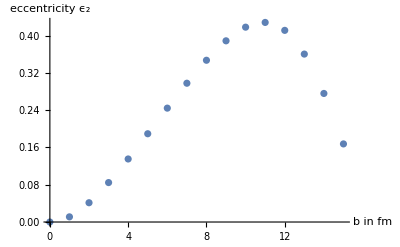
```mathematica
Show[-Graphics-,ListPlot[Transpose[{0.5*(bcls[[1;;-3,2]]+bcls[[2;;-2,2]]),δ2ls[[All,2]]}],PlotStyle->Red]]
```

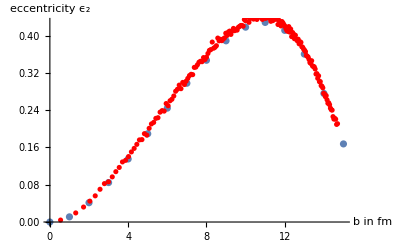

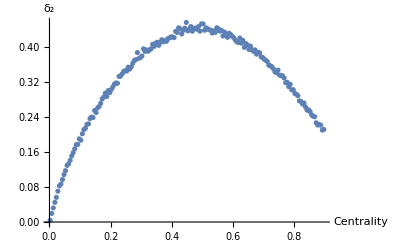

```mathematica
ListPlot[δ2ls,AxesLabel->{"Centrality", "δ_2"}]
```

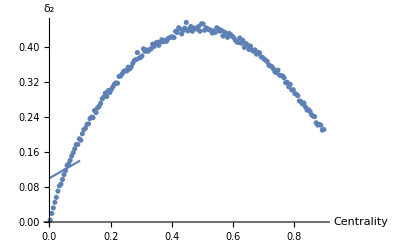

```mathematica
Show[-Graphics-,Plot[0.1+0.4*x,{x,0,0.1}]]
```

```mathematica
Rls=Table[{0.5*(bcls[[i,1]]+bcls[[i+1,1]]),Rrms[0.5*(bcls[[i,2]]+bcls[[i+1,2]])]},{i,1,Length[bcls]-2}]
```

{{0.0025,3.8338},{0.0075,3.67017},{0.0125,3.70051},{0.0175,3.60836},{0.0225,3.5843},{0.0275,3.55298},{0.0325,3.5449},{0.0375,3.58962},{0.0425,3.46714},{0.0475,3.46135},{0.0525,3.45734},{0.0575,3.42609},{0.0625,3.3747},{0.0675,3.4013},{0.0725,3.34009},{0.0775,3.31856},{0.0825,3.29369},{0.0875,3.29125},{0.0925,3.29652},{0.0975,3.25088},{0.1025,3.20464},{0.1075,3.19378},{0.1125,3.15051},{0.1175,3.15739},{0.1225,3.12829},{0.1275,3.135},{0.1325,3.09802},{0.1375,3.14554},{0.1425,3.08049},{0.1475,3.02414},{0.1525,3.05991},{0.1575,2.98706},{0.1625,2.9489},{0.1675,2.96328},{0.1725,3.00553},{0.1775,2.92948},{0.1825,2.93598},{0.1875,2.90098},{0.1925,2.91104},{0.1975,2.87954},{0.2025,2.8954},{0.2075,2.86075},{0.2125,2.83957},{0.2175,2.77478},{0.2225,2.82523},{0.2275,2.81438},{0.2325,2.78824},{0.2375,2.75931},{0.2425,2.78369},{0.2475,2.74369},{0.2525,2.71995},{0.2575,2.70587},{0.2625,2.68969},{0.2675,2.70148},{0.2725,2.65492},{0.2775,2.64587},{0.2825,2.66613},{0.2875,2.62434},{0.2925,2.59529},{0.2975,2.61945},{0.3025,2.59304},{0.3075,2.55972},{0.3125,2.55855},{0.3175,2.55241},{0.3225,2.52294},{0.3275,2.52157},{0.3325,2.47076},{0.3375,2.51157},{0.3425,2.47182},{0.3475,2.49912},{0.3525,2.43707},{0.3575,2.45937},{0.3625,2.41827},{0.3675,2.4528},{0.3725,2.42331},{0.3775,2.41359},{0.3825,2.40429},{0.3875,2.40861},{0.3925,2.35627},{0.3975,2.37232},{0.4025,2.40216},{0.4075,2.33718},{0.4125,2.32303},{0.4175,2.31484},{0.4225,2.34744},{0.4275,2.34244},{0.4325,2.29781},{0.4375,2.29588},{0.4425,2.3148},{0.4475,2.24145},{0.4525,2.29368},{0.4575,2.27096},{0.4625,2.28087},{0.4675,2.25432},{0.4725,2.21739},{0.4775,2.2466},{0.4825,2.22693},{0.4875,2.23754},{0.4925,2.2352},{0.4975,2.1985},{0.5025,2.18348},{0.5075,2.16728},{0.5125,2.17412},{0.5175,2.16835},{0.5225,2.16454},{0.5275,2.15375},{0.5325,2.1761},{0.5375,2.13235},{0.5425,2.13693},{0.5475,2.13204},{0.5525,2.11263},{0.5575,2.10926},{0.5625,2.13901},{0.5675,2.14902},{0.5725,2.08499},{0.5775,2.13124},{0.5825,2.06949},{0.5875,2.0967},{0.5925,2.10223},{0.5975,2.07287},{0.6025,2.1056},{0.6075,2.07606},{0.6125,2.07077},{0.6175,2.06573},{0.6225,2.08422},{0.6275,2.07821},{0.6325,2.05154},{0.6375,2.04468},{0.6425,2.05468},{0.6475,2.04366},{0.6525,2.04385},{0.6575,2.03611},{0.6625,2.04291},{0.6675,2.07833},{0.6725,2.04467},{0.6775,2.03991},{0.6825,2.03336},{0.6875,2.04885},{0.6925,2.03157},{0.6975,2.031},{0.7025,2.02165},{0.7075,2.04851},{0.7125,2.04342},{0.7175,2.00097},{0.7225,2.0256},{0.7275,2.04039},{0.7325,2.01953},{0.7375,2.04417},{0.7425,2.03615},{0.7475,2.02451},{0.7525,2.02967},{0.7575,2.02316},{0.7625,2.01941},{0.7675,2.04374},{0.7725,2.02986},{0.7775,2.05886},{0.7825,2.02715},{0.7875,2.05074},{0.7925,2.03251},{0.7975,2.07203},{0.8025,2.02846},{0.8075,2.05553},{0.8125,2.05739},{0.8175,2.03949},{0.8225,2.03391},{0.8275,2.06041},{0.8325,2.05634},{0.8375,2.06818},{0.8425,2.09089},{0.8475,2.06094},{0.8525,2.03527},{0.8575,2.09064},{0.8625,2.07943},{0.8675,2.05957},{0.8725,2.09134},{0.8775,2.05035},{0.8825,2.06391},{0.8875,2.06895},{0.8925,2.08171},{0.8975,2.08745}}

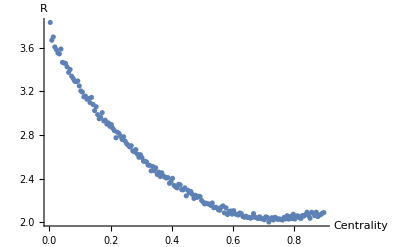

```mathematica
ListPlot[Rls,AxesLabel->{"Centrality", "R"}]
```

```mathematica
ϵ0[b_]:=TwsInterp[b/2]^2/TwsInterp[0]^2
```

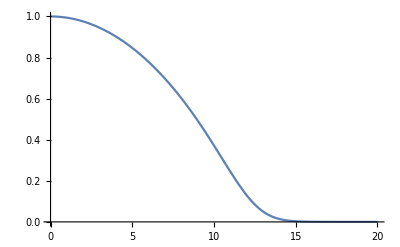

```mathematica
Plot[ϵ0[b],{b,0,20}]
```

```mathematica
ϵ0ls=Table[{0.5*(bcls[[i,1]]+bcls[[i+1,1]]),ϵ0[0.5*(bcls[[i,2]]+bcls[[i+1,2]])]},{i,1,Length[bcls]-2}]
```

{{0.0025,0.998179},{0.0075,0.989383},{0.0125,0.981963},{0.0175,0.974615},{0.0225,0.967287},{0.0275,0.959966},{0.0325,0.952647},{0.0375,0.945327},{0.0425,0.938004},{0.0475,0.930679},{0.0525,0.92335},{0.0575,0.916017},{0.0625,0.90868},{0.0675,0.901339},{0.0725,0.893993},{0.0775,0.886642},{0.0825,0.879285},{0.0875,0.871924},{0.0925,0.864557},{0.0975,0.857184},{0.1025,0.849806},{0.1075,0.842421},{0.1125,0.835031},{0.1175,0.827634},{0.1225,0.820231},{0.1275,0.812822},{0.1325,0.805405},{0.1375,0.797982},{0.1425,0.790552},{0.1475,0.783115},{0.1525,0.775671},{0.1575,0.768219},{0.1625,0.76076},{0.1675,0.753293},{0.1725,0.745818},{0.1775,0.738336},{0.1825,0.730846},{0.1875,0.723348},{0.1925,0.715842},{0.1975,0.708327},{0.2025,0.700805},{0.2075,0.693274},{0.2125,0.685735},{0.2175,0.678187},{0.2225,0.670631},{0.2275,0.663067},{0.2325,0.655495},{0.2375,0.647914},{0.2425,0.640325},{0.2475,0.632728},{0.2525,0.625122},{0.2575,0.617509},{0.2625,0.609888},{0.2675,0.602259},{0.2725,0.594623},{0.2775,0.58698},{0.2825,0.57933},{0.2875,0.571673},{0.2925,0.564009},{0.2975,0.55634},{0.3025,0.548665},{0.3075,0.540985},{0.3125,0.5333},{0.3175,0.525612},{0.3225,0.517919},{0.3275,0.510224},{0.3325,0.502527},{0.3375,0.494828},{0.3425,0.487128},{0.3475,0.479428},{0.3525,0.47173},{0.3575,0.464034},{0.3625,0.45634},{0.3675,0.448651},{0.3725,0.440967},{0.3775,0.43329},{0.3825,0.425621},{0.3875,0.41796},{0.3925,0.410311},{0.3975,0.402674},{0.4025,0.395051},{0.4075,0.387444},{0.4125,0.379854},{0.4175,0.372283},{0.4225,0.364733},{0.4275,0.357207},{0.4325,0.349706},{0.4375,0.342233},{0.4425,0.334789},{0.4475,0.327378},{0.4525,0.320001},{0.4575,0.312661},{0.4625,0.305361},{0.4675,0.298104},{0.4725,0.290891},{0.4775,0.283725},{0.4825,0.27661},{0.4875,0.26955},{0.4925,0.262544},{0.4975,0.255598},{0.5025,0.248714},{0.5075,0.241896},{0.5125,0.235145},{0.5175,0.228466},{0.5225,0.221861},{0.5275,0.215333},{0.5325,0.208885},{0.5375,0.202521},{0.5425,0.196243},{0.5475,0.190053},{0.5525,0.183954},{0.5575,0.177951},{0.5625,0.172045},{0.5675,0.166237},{0.5725,0.160532},{0.5775,0.154932},{0.5825,0.149438},{0.5875,0.144052},{0.5925,0.138778},{0.5975,0.133615},{0.6025,0.128567},{0.6075,0.123634},{0.6125,0.118817},{0.6175,0.114119},{0.6225,0.109539},{0.6275,0.105078},{0.6325,0.100738},{0.6375,0.0965177},{0.6425,0.0924181},{0.6475,0.0884389},{0.6525,0.0845799},{0.6575,0.0808406},{0.6625,0.0772205},{0.6675,0.0737189},{0.6725,0.0703347},{0.6775,0.0670666},{0.6825,0.0639134},{0.6875,0.0608739},{0.6925,0.0579463},{0.6975,0.0551287},{0.7025,0.0524192},{0.7075,0.0498159},{0.7125,0.0473171},{0.7175,0.0449199},{0.7225,0.0426221},{0.7275,0.0404212},{0.7325,0.0383156},{0.7375,0.0363019},{0.7425,0.0343776},{0.7475,0.0325401},{0.7525,0.030787},{0.7575,0.0291157},{0.7625,0.027523},{0.7675,0.0260064},{0.7725,0.0245631},{0.7775,0.023191},{0.7825,0.0218867},{0.7875,0.0206476},{0.7925,0.019471},{0.7975,0.0183546},{0.8025,0.017296},{0.8075,0.0162923},{0.8125,0.0153407},{0.8175,0.0144388},{0.8225,0.0135844},{0.8275,0.0127749},{0.8325,0.0120082},{0.8375,0.0112822},{0.8425,0.0105946},{0.8475,0.0099436},{0.8525,0.00932674},{0.8575,0.00874205},{0.8625,0.00818763},{0.8675,0.00766176},{0.8725,0.00716283},{0.8775,0.00668938},{0.8825,0.00624002},{0.8875,0.00581331},{0.8925,0.00540799},{0.8975,0.00502268}}

```mathematica
γhls=Table[{0.5*(bcls[[i,1]]+bcls[[i+1,1]]),Rls[[i,2]]^(3/4) ϵ0ls[[i,2]]^(1/4)},{i,1,Length[bcls]-2}]
```

{{0.0025,2.73857},{0.0075,2.64458},{0.0125,2.65595},{0.0175,2.6013},{0.0225,2.5834},{0.0275,2.56158},{0.0325,2.55233},{0.0375,2.57147},{0.0425,2.50052},{0.0475,2.49249},{0.0525,2.48541},{0.0575,2.46363},{0.0625,2.43097},{0.0675,2.44037},{0.0725,2.40244},{0.0775,2.38588},{0.0825,2.36753},{0.0875,2.36124},{0.0925,2.35907},{0.0975,2.32953},{0.1025,2.29967},{0.1075,2.28881},{0.1125,2.26054},{0.1175,2.25921},{0.1225,2.23854},{0.1275,2.23706},{0.1325,2.21216},{0.1375,2.23239},{0.1425,2.19254},{0.1475,2.15729},{0.1525,2.1712},{0.1575,2.12718},{0.1625,2.10163},{0.1675,2.10412},{0.1725,2.12129},{0.1775,2.07566},{0.1825,2.07382},{0.1875,2.04996},{0.1925,2.04993},{0.1975,2.02792},{0.2025,2.03087},{0.2075,2.00718},{0.2125,1.99057},{0.2175,1.95101},{0.2225,1.97202},{0.2275,1.96077},{0.2325,1.94151},{0.2375,1.92079},{0.2425,1.92782},{0.2475,1.90132},{0.2525,1.88327},{0.2575,1.87021},{0.2625,1.85605},{0.2675,1.8563},{0.2725,1.82641},{0.2775,1.81586},{0.2825,1.8203},{0.2875,1.79288},{0.2925,1.77199},{0.2975,1.77825},{0.3025,1.75867},{0.3075,1.73556},{0.3125,1.72878},{0.3175,1.71941},{0.3225,1.69823},{0.3275,1.6912},{0.3325,1.65925},{0.3375,1.6733},{0.3425,1.64692},{0.3475,1.65395},{0.3525,1.6165},{0.3575,1.6209},{0.3625,1.59386},{0.3675,1.60407},{0.3725,1.58273},{0.3775,1.57106},{0.3825,1.55954},{0.3875,1.55456},{0.3925,1.52212},{0.3975,1.52271},{0.4025,1.52973},{0.4075,1.49132},{0.4125,1.47722},{0.4175,1.46592},{0.4225,1.4738},{0.4275,1.4638},{0.4325,1.43519},{0.4375,1.42657},{0.4425,1.42751},{0.4475,1.38567},{0.4525,1.4018},{0.4575,1.38333},{0.4625,1.37968},{0.4675,1.35942},{0.4725,1.33448},{0.4775,1.33927},{0.4825,1.32205},{0.4875,1.31822},{0.4925,1.30854},{0.4975,1.28376},{0.5025,1.26849},{0.5075,1.25269},{0.5125,1.2468},{0.5175,1.23538},{0.5225,1.22474},{0.5275,1.21108},{0.5325,1.21126},{0.5375,1.18375},{0.5425,1.17636},{0.5475,1.16497},{0.5525,1.14761},{0.5575,1.13677},{0.5625,1.13912},{0.5675,1.13334},{0.5725,1.09829},{0.5775,1.10665},{0.5825,1.07279},{0.5875,1.07345},{0.5925,1.06559},{0.5975,1.04446},{0.6025,1.04668},{0.6075,1.02557},{0.6125,1.01349},{0.6175,1.00149},{0.6225,0.997931},{0.6275,0.985476},{0.6325,0.965736},{0.6375,0.953063},{0.6425,0.94623},{0.6475,0.932112},{0.6525,0.921835},{0.6575,0.908885},{0.6625,0.900783},{0.6675,0.901947},{0.6725,0.880563},{0.6775,0.86863},{0.6825,0.856167},{0.6875,0.850628},{0.6925,0.834893},{0.6975,0.824378},{0.7025,0.811246},{0.7075,0.808949},{0.7125,0.797117},{0.7175,0.774534},{0.7225,0.771477},{0.7275,0.765486},{0.7325,0.749517},{0.7375,0.746225},{0.7425,0.733967},{0.7475,0.720851},{0.7525,0.712296},{0.7575,0.700736},{0.7625,0.689989},{0.7675,0.68642},{0.7725,0.673241},{0.7775,0.670733},{0.7825,0.653447},{0.7875,0.649606},{0.7925,0.635874},{0.7975,0.635672},{0.8025,0.616399},{0.8075,0.613322},{0.8125,0.604572},{0.8175,0.591594},{0.8225,0.581445},{0.8275,0.578169},{0.8325,0.568447},{0.8375,0.562068},{0.8425,0.557853},{0.8475,0.543168},{0.8525,0.52954},{0.8575,0.531634},{0.8625,0.520892},{0.8675,0.508645},{0.8725,0.505929},{0.8775,0.490025},{0.8825,0.483966},{0.8875,0.476341},{0.8925,0.469975},{0.8975,0.462324}}

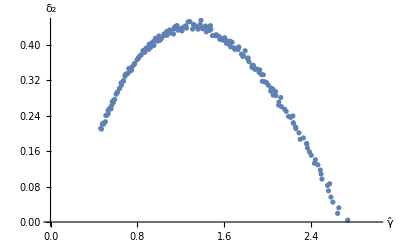

```mathematica
ListPlot[Table[{Rls[[i,2]]^(3/4) ϵ0ls[[i,2]]^(1/4),δ2ls[[i,2]]},{i,1,Length[δ2ls]}],PlotRange->{{0,3},{0,0.45}},AxesLabel->{ "γ̂","δ_2"}]
```

```mathematica
Needs["ErrorBarPlots`"]
```

### DATA

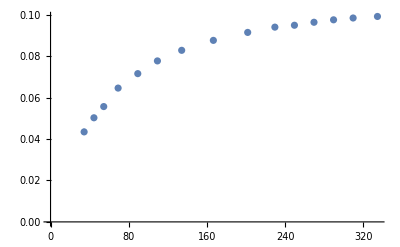

```mathematica
(* PbPb,v22,peripheral subtraction:24.3 0.03562 0.002246*)
v22cms={{34.34,0.04343,0.001494},{44.37,0.05024,0.001111},{54.39,0.05565,0.0008841},{69.1,0.06457 ,0.0005586},{89.21,0.07154,0.0004248},{109.3,0.07768,0.0003413},{134.1,0.08279 ,0.0002575},{166.5,0.08759,0.0002047},{201.6,0.09143,0.0001702},{229.4,0.09398,0.0001683},{249.4,0.09489,0.0001576},{269.4,0.09633,0.0001469},{289.4,0.09751,0.0001375},{309.4,0.09839,0.0001311},{334.3,0.09913,0.0001118}};
ErrorListPlot[%]
```

N_(trk offline), signal strength v_2{4}, statistical + systematic errors

```mathematica
v24cms=Import["v24cmsntrack.dat"]
```

{{34.34,0.0398,0.01727,0.001194},{44.37,0.05425,0.005501,0.001627},{54.39,0.05399,0.004521,0.00162},{69.11,0.05996,0.001912,0.001799},{89.21,0.0641,0.001249,0.001923},{109.3,0.06684,0.0009372,0.002005},{134.1,0.07102,0.0005783,0.002131},{166.5,0.07426,0.0004147,0.002228},{201.6,0.07692,0.000347,0.002308},{229.4,0.07842,0.0004179,0.002353},{249.4,0.08031,0.0003848,0.002409},{269.4,0.08057,0.000382,0.002417},{289.4,0.08251,0.0003449,0.002475},{309.4,0.08261,0.0003349,0.002478},{334.3,0.08355,0.0002693,0.002507}}

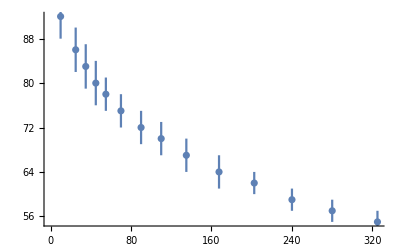

InterpolatingFunction[{{10., 325.}}, <>]

```mathematica
NtrackvsCent={{10.,92.,4.},{25.,86.,4.},{35., 83., 4.},{45.,80.,4.}, {55.,78.,3.},{70.,75.,3.},{90.,72.,3.},{110.,70.,3.},{135.,67.,3.},{167.5,64.,3.},{202.5,62.,2.},{240.,59.,2.},{280.,57.,2.},{325.,55.,2.}};
ErrorListPlot[%]
ntrackcent=Interpolation[Table[{NtrackvsCent[[n]][[1]],0.01*NtrackvsCent[[n]][[2]]},{n,1,14}]]
```

InterpolatingFunction::dmval: Input value {334.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{0.544946,0.08355},{0.55747,0.08261},{0.566038,0.08251},{0.574641,0.08057},{0.584541,0.08031},{0.598277,0.07842},{0.620517,0.07692},{0.640764,0.07426},{0.671062,0.07102},{0.70067,0.06684},{0.720985,0.0641},{0.751684,0.05996},{0.781092,0.05399},{0.801699,0.05425},{0.831905,0.0398}}

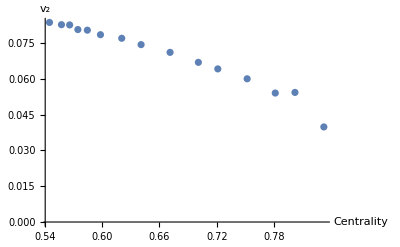

```mathematica
(* v22cmscentrality=Table[{ntrackcent[v22cms[[i,1]]],v22cms[[i,2]]},{i,Length[v22cms],1,-1}]*)
v24cmscentrality=Table[{ntrackcent[v24cms[[i,1]]],v24cms[[i,2]]},{i,Length[v24cms],1,-1}]
(* ListPlot[v22cmscentrality,AxesLabel->{"Centrality","v_2"}]*)
ListPlot[v24cmscentrality,AxesLabel->{"Centrality","v_2"}]
```

```mathematica
v22a={{2.50,.027073,0.000133},{7.50,.044243,0.000123},{15.00,.063946,0.000097},{25.00,.083069,0.000115},{35.00,.094703,0.000144},{45.00,.099279,0.000198},{55.00,.096305,0.000317},{65.00,.087083,0.000755},{75.00,.070515,0.009428}};
```

```mathematica
v22cmscentrality=Join[v22cmscentrality,Transpose[{0.01*v22a[[All,1]],v22a[[All,2]]}]]
```

{{0.544946,0.09913},{0.55747,0.09839},{0.566038,0.09751},{0.574641,0.09633},{0.584541,0.09489},{0.598277,0.09398},{0.620517,0.09143},{0.640764,0.08759},{0.671062,0.08279},{0.70067,0.07768},{0.720985,0.07154},{0.751703,0.06457},{0.781092,0.05565},{0.801699,0.05024},{0.831905,0.04343},{0.025,0.027073},{0.075,0.044243},{0.15,0.063946},{0.25,0.083069},{0.35,0.094703},{0.45,0.099279},{0.55,0.096305},{0.65,0.087083},{0.75,0.070515}}

```mathematica
v24alice276=Import["v24alice276fine.dat"];
v22alice276=Import["v22alice276fine.dat"];
```

```mathematica
(*As a function of centrality*)
δ2Interp=Interpolation[δ2ls]
γhInterp=Interpolation[γhls]
```

InterpolatingFunction[{{0.0025, 0.8975}}, <>]

InterpolatingFunction[{{0.0025, 0.8975}}, <>]

```mathematica
v24alice276
```

{{4.5,4,5,0.0231417,0.000320813,-0.000320813,0.000675783,-0.000675783},{5.5,5,6,0.0270559,0.000246752,-0.000246752,0.000516816,-0.000516816},{6.5,6,7,0.0310327,0.000214805,-0.000214805,0.000416104,-0.000416104},{7.5,7,8,0.0349283,0.000177376,-0.000177376,0.000891717,-0.000891717},{8.5,8,9,0.0378281,0.000156293,-0.000156293,0.000637884,-0.000637884},{9.5,9,10,0.0410019,0.000159447,-0.000159447,0.000500866,-0.000500866},{10.5,10,11,0.0438482,0.000149483,-0.000149483,0.000490179,-0.000490179},{11.5,11,12,0.0467624,0.000142366,-0.000142366,0.000564033,-0.000564033},{12.5,12,13,0.0494411,0.000137234,-0.000137234,0.000548889,-0.000548889},{13.5,13,14,0.0517866,0.000131535,-0.000131535,0.000636876,-0.000636876},{14.5,14,15,0.0544597,0.000135205,-0.000135205,0.000567475,-0.000567475},{15.5,15,16,0.0566431,0.000137378,-0.000137378,0.000515459,-0.000515459},{16.5,16,17,0.0584664,0.000140102,-0.000140102,0.000394888,-0.000394888},{17.5,17,18,0.0607589,0.000138403,-0.000138403,0.000543795,-0.000543795},{18.5,18,19,0.0622534,0.000153882,-0.000153882,0.000507785,-0.000507785},{19.5,19,20,0.064197,0.000149195,-0.000149195,0.000531484,-0.000531484},{20.5,20,21,0.0659792,0.000136262,-0.000136262,0.000502008,-0.000502008},{21.5,21,22,0.0678528,0.000145923,-0.000145923,0.000463361,-0.000463361},{22.5,22,23,0.069217,0.00014924,-0.00014924,0.000463202,-0.000463202},{23.5,23,24,0.070572,0.000153567,-0.000153567,0.000578974,-0.000578974},{24.5,24,25,0.0720594,0.000151426,-0.000151426,0.000696455,-0.000696455},{25.5,25,26,0.0731888,0.000149775,-0.000149775,0.00072366,-0.00072366},{26.5,26,27,0.0746239,0.000162947,-0.000162947,0.00056745,-0.00056745},{27.5,27,28,0.0752492,0.000154201,-0.000154201,0.000578528,-0.000578528},{28.5,28,29,0.0767561,0.000156757,-0.000156757,0.000612109,-0.000612109},{29.5,29,30,0.0773589,0.000171805,-0.000171805,0.000697075,-0.000697075},{30.5,30,31,0.0785844,0.000160015,-0.000160015,0.000758981,-0.000758981},{31.5,31,32,0.0794191,0.000177193,-0.000177193,0.000727841,-0.000727841},{32.5,32,33,0.0799349,0.000188335,-0.000188335,0.000774645,-0.000774645},{33.5,33,34,0.0809039,0.000187487,-0.000187487,0.00083514,-0.00083514},{34.5,34,35,0.0814048,0.000181596,-0.000181596,0.000822905,-0.000822905},{35.5,35,36,0.0817442,0.000189367,-0.000189367,0.000655453,-0.000655453},{36.5,36,37,0.0825543,0.000213891,-0.000213891,0.00094776,-0.00094776},{37.5,37,38,0.0826957,0.000205235,-0.000205235,0.000867004,-0.000867004},{38.5,38,39,0.0829038,0.000223766,-0.000223766,0.000946625,-0.000946625},{39.5,39,40,0.0832086,0.000221785,-0.000221785,0.00112075,-0.00112075},{40.5,40,41,0.082805,0.000250826,-0.000250826,0.000928236,-0.000928236},{41.5,41,42,0.0830872,0.000253934,-0.000253934,0.00106914,-0.00106914},{42.5,42,43,0.0830305,0.000278518,-0.000278518,0.00106939,-0.00106939},{43.5,43,44,0.0835025,0.000275172,-0.000275172,0.00107026,-0.00107026},{44.5,44,45,0.0826034,0.000289509,-0.000289509,0.00108996,-0.00108996},{45.5,45,46,0.0827479,0.000310117,-0.000310117,0.00087217,-0.00087217},{46.5,46,47,0.0825109,0.000320553,-0.000320553,0.00104037,-0.00104037},{47.5,47,48,0.0825787,0.000361021,-0.000361021,0.000930215,-0.000930215},{48.5,48,49,0.0813734,0.000393433,-0.000393433,0.000992716,-0.000992716},{49.5,49,50,0.081965,0.000393603,-0.000393603,0.000894596,-0.000894596},{50.5,50,51,0.0806924,0.000447233,-0.000447233,0.000897945,-0.000897945},{51.5,51,52,0.0800419,0.000467072,-0.000467072,0.000962371,-0.000962371},{52.5,52,53,0.0794265,0.000511351,-0.000511351,0.000849914,-0.000849914},{53.5,53,54,0.0799981,0.000549976,-0.000549976,0.000962007,-0.000962007},{54.5,54,55,0.077468,0.000669922,-0.000669922,0.000850318,-0.000850318},{55.5,55,56,0.0771395,0.000704297,-0.000704297,0.000883417,-0.000883417},{56.5,56,57,0.0764263,0.000755082,-0.000755082,0.000916998,-0.000916998},{57.5,57,58,0.0752334,0.000838519,-0.000838519,0.000882451,-0.000882451},{58.5,58,59,0.07408,0.000927003,-0.000927003,0.000848864,-0.000848864},{59.5,59,60,0.0738994,0.0010454,-0.0010454,0.00105028,-0.00105028},{61.,60,62,0.0719562,0.000901386,-0.000901386,0.000954284,-0.000954284},{63.,62,64,0.0686352,0.00133231,-0.00133231,0.000942512,-0.000942512},{65.,64,66,0.0673931,0.00166374,-0.00166374,0.000909889,-0.000909889},{67.,66,68,0.0643767,0.00247489,-0.00247489,0.000930279,-0.000930279},{69.,68,70,0.0636715,0.00313028,-0.00313028,0.000924388,-0.000924388},{}}

```mathematica
v24alice276[[1,2]]
```

4

```mathematica
Final24cms=Table[{γhInterp[v24cmscentrality[[i,1]]],v24cmscentrality[[i,2]]/δ2Interp[v24cmscentrality[[i,1]]]},{i,1,Length[v24cmscentrality]}]
Final24=Table[{γhInterp[0.01*v24alice276[[i,1]]],v24alice276[[i,4]]/δ2Interp[0.01*v24alice276[[i,1]]]},{i,1,Length[v24alice276]-1}]
Final22=Table[{γhInterp[0.01*v22alice276[[i,1]]],v22alice276[[i,4]]/δ2Interp[0.01*v22alice276[[i,1]]]},{i,1,Length[v22alice276]-1}]
```

{{1.17141,0.190997},{1.1368,0.189876},{1.13712,0.193152},{1.10155,0.186968},{1.07133,0.189151},{1.04445,0.185304},{0.999439,0.184822},{0.948761,0.184158},{0.887151,0.181227},{0.815507,0.179478},{0.771683,0.180039},{0.713697,0.178054},{0.658173,0.173658},{0.619313,0.184401},{0.56962,0.146748}}

{{2.49251,0.225614},{2.47612,0.219222},{2.436,0.228184},{2.39294,0.226336},{2.36337,0.21996},{2.34603,0.223444},{2.29414,0.227212},{2.2594,0.220378},{2.23806,0.221721},{2.22321,0.217337},{2.17155,0.220989},{2.15166,0.222632},{2.10021,0.219294},{2.09966,0.214777},{2.06178,0.214842},{2.03874,0.215569},{2.02024,0.216102},{1.96844,0.214663},{1.96891,0.213616},{1.92951,0.210817},{1.91614,0.2092},{1.8765,0.209866},{1.85715,0.212895},{1.81899,0.205899},{1.80818,0.20246},{1.77504,0.207369},{1.74632,0.202944},{1.72499,0.203412},{1.69538,0.204622},{1.66593,0.201948},{1.65113,0.201656},{1.61805,0.201363},{1.59861,0.199679},{1.57628,0.200748},{1.55836,0.199899},{1.51995,0.197667},{1.51185,0.197031},{1.47019,0.191639},{1.47108,0.187491},{1.42903,0.193425},{1.40564,0.183559},{1.3938,0.189723},{1.37088,0.187456},{1.3364,0.186658},{1.31966,0.183661},{1.2965,0.185116},{1.26,0.181769},{1.24139,0.181136},{1.21724,0.181363},{1.19798,0.184702},{1.17129,0.177042},{1.14096,0.176303},{1.13857,0.177709},{1.1024,0.174802},{1.07149,0.174086},{1.0544,0.173676},{1.01896,0.174303},{0.97562,0.166919},{0.9269,0.169425},{0.892074,0.164599},{0.843072,0.167136}}

{{2.66769,1.65195},{2.63046,0.608335},{2.57195,0.424709},{2.56576,0.358784},{2.49251,0.328741},{2.47612,0.305927},{2.436,0.300401},{2.39294,0.286892},{2.36337,0.273816},{2.34603,0.272996},{2.29414,0.27582},{2.2594,0.261741},{2.23806,0.261989},{2.22321,0.254931},{2.17155,0.257481},{2.15166,0.257642},{2.10021,0.254092},{2.09966,0.247082},{2.06178,0.24743},{2.03874,0.247122},{2.02024,0.24717},{1.96844,0.244267},{1.96891,0.243819},{1.92951,0.240091},{1.91614,0.23816},{1.8765,0.239488},{1.85715,0.242644},{1.81899,0.235652},{1.80818,0.230219},{1.77504,0.237501},{1.74632,0.231238},{1.72499,0.231558},{1.69538,0.234334},{1.66593,0.231636},{1.65113,0.230717},{1.61805,0.231876},{1.59861,0.229059},{1.57628,0.231529},{1.55836,0.231764},{1.51995,0.229115},{1.51185,0.230508},{1.47019,0.224214},{1.47108,0.220302},{1.42903,0.227394},{1.40564,0.217414},{1.3938,0.22501},{1.37088,0.222514},{1.3364,0.221742},{1.31966,0.219839},{1.2965,0.220808},{1.26,0.219795},{1.24139,0.220095},{1.21724,0.219082},{1.19798,0.222697},{1.17129,0.219681},{1.14096,0.218274},{1.13857,0.2206},{1.1024,0.21707},{1.07149,0.218519},{1.0544,0.217282},{1.01896,0.219327},{0.97562,0.218075},{0.9269,0.219841},{0.892074,0.214377},{0.843072,0.213794},{0.769289,0.217054},{0.672244,0.216366}}

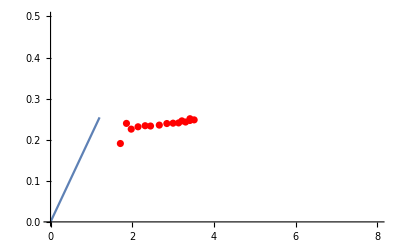

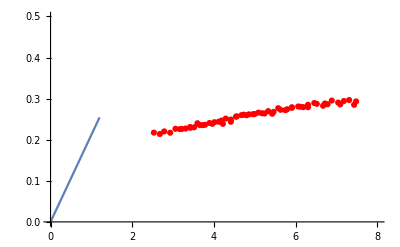

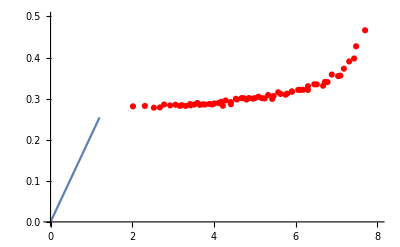

```mathematica
p24cms=Show[ListPlot[Transpose[{3.0*Final24cms[[All,1]],1.3*Final24cms[[All,2]]}],PlotRange->{{0,8.0},{0.,0.5}},PlotStyle->Red],Plot[0.212*x,{x,0,1.2}]]
p24=Show[ListPlot[Transpose[{3.0*Final24[[All,1]],1.3*Final24[[All,2]]}],PlotRange->{{0,8.0},{0.,0.5}},PlotStyle->Red],Plot[0.212*x,{x,0,1.2}]]
p22=Show[ListPlot[Transpose[{3.0*Final22[[All,1]],1.3*Final22[[All,2]]}],PlotRange->{{0,8.0},{0.,0.5}},PlotStyle->Red],Plot[0.212*x,{x,0,1.2}]]
```

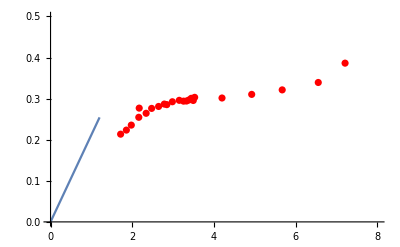

```mathematica
Show[ListPlot[Transpose[{3.0*Final[[All,1]],1.3*Final[[All,2]]}],PlotRange->{{0,8.0},{0.,0.5}},PlotStyle->Red],Plot[0.212*x,{x,0,1.2}]]
```

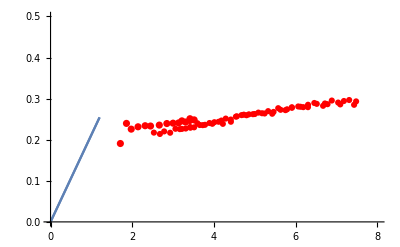

```mathematica
Show[-Graphics-,-Graphics-]
```

```mathematica
3.0 (ϵ0τ0)^(1/4)
```

```mathematica
81./fm^3
```

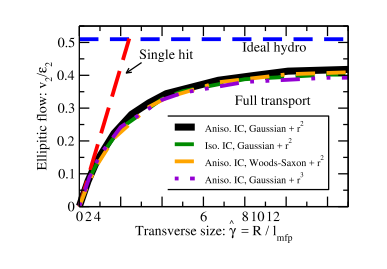

```mathematica
Import["v2.pdf"]
```

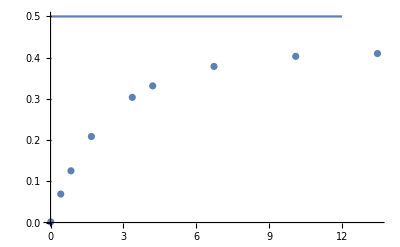

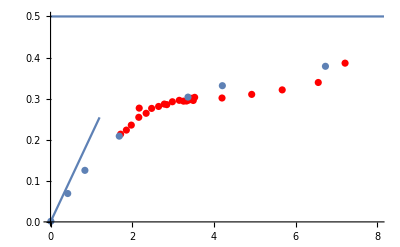

```mathematica
Show[-Graphics-,-Graphics-]
```

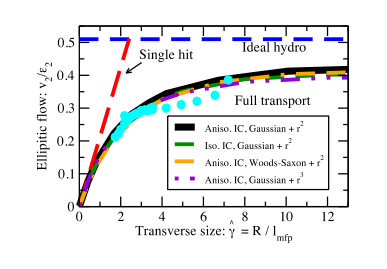

```mathematica
Import["v2.pdf"]
```

```mathematica
0.11/0.2
```

```mathematica
0.55*(3.7)^(3/4)(300.)^(1/4)
```

6.10653

```mathematica
Import["v22alice276fine.dat"]
Import["v24alice276fine.dat"]
```

{{0.5,0,1,0.0203831,0.000139745,-0.000139745,0.000482763,-0.000482763},{1.5,1,2,0.023451,0.000133288,-0.000133288,0.000427145,-0.000427145},{2.5,2,3,0.0268318,0.000126444,-0.000126444,0.000619586,-0.000619586},{3.5,3,4,0.0303036,0.000122356,-0.000122356,0.000396529,-0.000396529},{4.5,4,5,0.0337196,0.000118285,-0.000118285,0.00044808,-0.00044808},{5.5,5,6,0.0377568,0.000115605,-0.000115605,0.000634909,-0.000634909},{6.5,6,7,0.0408539,0.00011638,-0.00011638,0.000662644,-0.000662644},{7.5,7,8,0.0442734,0.000115902,-0.000115902,0.000679147,-0.000679147},{8.5,8,9,0.0470901,0.00011547,-0.00011547,0.000672767,-0.000672767},{9.5,9,10,0.0500947,0.00011732,-0.00011732,0.000636969,-0.000636969},{10.5,10,11,0.0532288,0.000117555,-0.000117555,0.000690571,-0.000690571},{11.5,11,12,0.0555394,0.000119179,-0.000119179,0.000631858,-0.000631858},{12.5,12,13,0.0584203,0.000119859,-0.000119859,0.000436354,-0.000436354},{13.5,13,14,0.0607444,0.000121298,-0.000121298,0.000646142,-0.000646142},{14.5,14,15,0.0634526,0.000123625,-0.000123625,0.000498538,-0.000498538},{15.5,15,16,0.0655505,0.000126066,-0.000126066,0.000445894,-0.000445894},{16.5,16,17,0.0677441,0.000128221,-0.000128221,0.000405631,-0.000405631},{17.5,17,18,0.0698978,0.000129933,-0.000129933,0.000550933,-0.000550933},{18.5,18,19,0.0716964,0.000134753,-0.000134753,0.000452621,-0.000452621},{19.5,19,20,0.0735935,0.000135788,-0.000135788,0.000647342,-0.000647342},{20.5,20,21,0.0754647,0.000136766,-0.000136766,0.000525608,-0.000525608},{21.5,21,22,0.0772104,0.000140256,-0.000140256,0.000535348,-0.000535348},{22.5,22,23,0.0790037,0.000143119,-0.000143119,0.000549031,-0.000549031},{23.5,23,24,0.0803718,0.000146519,-0.000146519,0.000542809,-0.000542809},{24.5,24,25,0.0820346,0.000149344,-0.000149344,0.00069314,-0.00069314},{25.5,25,26,0.0835195,0.000151543,-0.000151543,0.000773063,-0.000773063},{26.5,26,27,0.0850518,0.000155507,-0.000155507,0.000823548,-0.000823548},{27.5,27,28,0.0861233,0.000157687,-0.000157687,0.000718528,-0.000718528},{28.5,28,29,0.08728,0.000161121,-0.000161121,0.000725109,-0.000725109},{29.5,29,30,0.0885997,0.000167003,-0.000167003,0.000899731,-0.000899731},{30.5,30,31,0.0895405,0.000168712,-0.000168712,0.000952477,-0.000952477},{31.5,31,32,0.0904081,0.000174537,-0.000174537,0.00109132,-0.00109132},{32.5,32,33,0.0915419,0.000180179,-0.000180179,0.00109033,-0.00109033},{33.5,33,34,0.0927974,0.000183738,-0.000183738,0.00102634,-0.00102634},{34.5,34,35,0.0931361,0.000186725,-0.000186725,0.000903104,-0.000903104},{35.5,35,36,0.0941309,0.000191501,-0.000191501,0.00105055,-0.00105055},{36.5,36,37,0.094701,0.000200416,-0.000200416,0.00108448,-0.00108448},{37.5,37,38,0.0953757,0.000202218,-0.000202218,0.00110703,-0.00110703},{38.5,38,39,0.0961196,0.000210416,-0.000210416,0.00115789,-0.00115789},{39.5,39,40,0.0964466,0.000215964,-0.000215964,0.000915726,-0.000915726},{40.5,40,41,0.0968742,0.000225032,-0.000225032,0.00107473,-0.00107473},{41.5,41,42,0.0972107,0.000231434,-0.000231434,0.000958271,-0.000958271},{42.5,42,43,0.0975607,0.000240103,-0.000240103,0.000920701,-0.000920701},{43.5,43,44,0.0981672,0.000245642,-0.000245642,0.000974485,-0.000974485},{44.5,44,45,0.0978385,0.000253653,-0.000253653,0.000944076,-0.000944076},{45.5,45,46,0.098138,0.000264074,-0.000264074,0.00103569,-0.00103569},{46.5,46,47,0.0979422,0.000274171,-0.000274171,0.00117269,-0.00117269},{47.5,47,48,0.0981,0.000287612,-0.000287612,0.000950893,-0.000950893},{48.5,48,49,0.0974023,0.000301824,-0.000301824,0.000975702,-0.000975702},{49.5,49,50,0.0977683,0.000311228,-0.000311228,0.000979037,-0.000979037},{50.5,50,51,0.0975734,0.000327021,-0.000327021,0.000980789,-0.000980789},{51.5,51,52,0.0972574,0.00034095,-0.00034095,0.00095015,-0.00095015},{52.5,52,53,0.0959453,0.000360839,-0.000360839,0.00108078,-0.00108078},{53.5,53,54,0.0964546,0.000380175,-0.000380175,0.000961975,-0.000961975},{54.5,54,55,0.0961252,0.000401672,-0.000401672,0.00104452,-0.00104452},{55.5,55,56,0.0955035,0.000423823,-0.000423823,0.0011255,-0.0011255},{56.5,56,57,0.0948725,0.000442532,-0.000442532,0.00106084,-0.00106084},{57.5,57,58,0.0934254,0.000474229,-0.000474229,0.00106186,-0.00106186},{58.5,58,59,0.0929879,0.000500259,-0.000500259,0.0010458,-0.0010458},{59.5,59,60,0.0924541,0.000543023,-0.000543023,0.000949899,-0.000949899},{61.,60,62,0.0905434,0.000427167,-0.000427167,0.00102082,-0.00102082},{63.,62,64,0.0896699,0.00050018,-0.00050018,0.00111038,-0.00111038},{65.,64,66,0.0874471,0.000618973,-0.000618973,0.000968122,-0.000968122},{67.,66,68,0.0838455,0.000782451,-0.000782451,0.00090669,-0.00090669},{69.,68,70,0.081446,0.000941939,-0.000941939,0.000954348,-0.000954348},{72.5,70,75,0.077089,0.000821076,-0.000821076,0.00101762,-0.00101762},{77.5,75,80,0.0688025,0.00139719,-0.00139719,0.000937563,-0.000937563},{}}

{{4.5,4,5,0.0231417,0.000320813,-0.000320813,0.000675783,-0.000675783},{5.5,5,6,0.0270559,0.000246752,-0.000246752,0.000516816,-0.000516816},{6.5,6,7,0.0310327,0.000214805,-0.000214805,0.000416104,-0.000416104},{7.5,7,8,0.0349283,0.000177376,-0.000177376,0.000891717,-0.000891717},{8.5,8,9,0.0378281,0.000156293,-0.000156293,0.000637884,-0.000637884},{9.5,9,10,0.0410019,0.000159447,-0.000159447,0.000500866,-0.000500866},{10.5,10,11,0.0438482,0.000149483,-0.000149483,0.000490179,-0.000490179},{11.5,11,12,0.0467624,0.000142366,-0.000142366,0.000564033,-0.000564033},{12.5,12,13,0.0494411,0.000137234,-0.000137234,0.000548889,-0.000548889},{13.5,13,14,0.0517866,0.000131535,-0.000131535,0.000636876,-0.000636876},{14.5,14,15,0.0544597,0.000135205,-0.000135205,0.000567475,-0.000567475},{15.5,15,16,0.0566431,0.000137378,-0.000137378,0.000515459,-0.000515459},{16.5,16,17,0.0584664,0.000140102,-0.000140102,0.000394888,-0.000394888},{17.5,17,18,0.0607589,0.000138403,-0.000138403,0.000543795,-0.000543795},{18.5,18,19,0.0622534,0.000153882,-0.000153882,0.000507785,-0.000507785},{19.5,19,20,0.064197,0.000149195,-0.000149195,0.000531484,-0.000531484},{20.5,20,21,0.0659792,0.000136262,-0.000136262,0.000502008,-0.000502008},{21.5,21,22,0.0678528,0.000145923,-0.000145923,0.000463361,-0.000463361},{22.5,22,23,0.069217,0.00014924,-0.00014924,0.000463202,-0.000463202},{23.5,23,24,0.070572,0.000153567,-0.000153567,0.000578974,-0.000578974},{24.5,24,25,0.0720594,0.000151426,-0.000151426,0.000696455,-0.000696455},{25.5,25,26,0.0731888,0.000149775,-0.000149775,0.00072366,-0.00072366},{26.5,26,27,0.0746239,0.000162947,-0.000162947,0.00056745,-0.00056745},{27.5,27,28,0.0752492,0.000154201,-0.000154201,0.000578528,-0.000578528},{28.5,28,29,0.0767561,0.000156757,-0.000156757,0.000612109,-0.000612109},{29.5,29,30,0.0773589,0.000171805,-0.000171805,0.000697075,-0.000697075},{30.5,30,31,0.0785844,0.000160015,-0.000160015,0.000758981,-0.000758981},{31.5,31,32,0.0794191,0.000177193,-0.000177193,0.000727841,-0.000727841},{32.5,32,33,0.0799349,0.000188335,-0.000188335,0.000774645,-0.000774645},{33.5,33,34,0.0809039,0.000187487,-0.000187487,0.00083514,-0.00083514},{34.5,34,35,0.0814048,0.000181596,-0.000181596,0.000822905,-0.000822905},{35.5,35,36,0.0817442,0.000189367,-0.000189367,0.000655453,-0.000655453},{36.5,36,37,0.0825543,0.000213891,-0.000213891,0.00094776,-0.00094776},{37.5,37,38,0.0826957,0.000205235,-0.000205235,0.000867004,-0.000867004},{38.5,38,39,0.0829038,0.000223766,-0.000223766,0.000946625,-0.000946625},{39.5,39,40,0.0832086,0.000221785,-0.000221785,0.00112075,-0.00112075},{40.5,40,41,0.082805,0.000250826,-0.000250826,0.000928236,-0.000928236},{41.5,41,42,0.0830872,0.000253934,-0.000253934,0.00106914,-0.00106914},{42.5,42,43,0.0830305,0.000278518,-0.000278518,0.00106939,-0.00106939},{43.5,43,44,0.0835025,0.000275172,-0.000275172,0.00107026,-0.00107026},{44.5,44,45,0.0826034,0.000289509,-0.000289509,0.00108996,-0.00108996},{45.5,45,46,0.0827479,0.000310117,-0.000310117,0.00087217,-0.00087217},{46.5,46,47,0.0825109,0.000320553,-0.000320553,0.00104037,-0.00104037},{47.5,47,48,0.0825787,0.000361021,-0.000361021,0.000930215,-0.000930215},{48.5,48,49,0.0813734,0.000393433,-0.000393433,0.000992716,-0.000992716},{49.5,49,50,0.081965,0.000393603,-0.000393603,0.000894596,-0.000894596},{50.5,50,51,0.0806924,0.000447233,-0.000447233,0.000897945,-0.000897945},{51.5,51,52,0.0800419,0.000467072,-0.000467072,0.000962371,-0.000962371},{52.5,52,53,0.0794265,0.000511351,-0.000511351,0.000849914,-0.000849914},{53.5,53,54,0.0799981,0.000549976,-0.000549976,0.000962007,-0.000962007},{54.5,54,55,0.077468,0.000669922,-0.000669922,0.000850318,-0.000850318},{55.5,55,56,0.0771395,0.000704297,-0.000704297,0.000883417,-0.000883417},{56.5,56,57,0.0764263,0.000755082,-0.000755082,0.000916998,-0.000916998},{57.5,57,58,0.0752334,0.000838519,-0.000838519,0.000882451,-0.000882451},{58.5,58,59,0.07408,0.000927003,-0.000927003,0.000848864,-0.000848864},{59.5,59,60,0.0738994,0.0010454,-0.0010454,0.00105028,-0.00105028},{61.,60,62,0.0719562,0.000901386,-0.000901386,0.000954284,-0.000954284},{63.,62,64,0.0686352,0.00133231,-0.00133231,0.000942512,-0.000942512},{65.,64,66,0.0673931,0.00166374,-0.00166374,0.000909889,-0.000909889},{67.,66,68,0.0643767,0.00247489,-0.00247489,0.000930279,-0.000930279},{69.,68,70,0.0636715,0.00313028,-0.00313028,0.000924388,-0.000924388},{}}

```mathematica
0.8^3
```

0.512

In the CMS-publication 1312.1845, there is a plot in the supplementary material which shows ϵ_2{2} as a function of impact parameter, calculated from the “Phobos Glauber model” for PbPb collisions at the LHC. Digitizing this plot, we obtain a function dependence for which fluctuations regulate the behavior in the ultra-central and ultra-peripheral bins

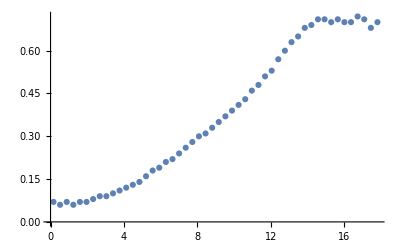

```mathematica
phobosGlauberCMS={{0.16,0.07},{0.52,0.06},{0.88,0.07},{1.24,0.06},{1.5999999999999999,0.07},{1.9599999999999997,0.07},{2.3200000000000003,0.08},{2.68,0.09},{3.04,0.09},{3.4,0.1},{3.76,0.11},{4.12,0.12},{4.48,0.13},{4.84,0.14},{5.2,0.16},{5.56,0.18},{5.92,0.19},{6.28,0.21},{6.64,0.22},{7.,0.24},{7.359999999999999,0.26},{7.72,0.28},{8.08,0.30},{8.44,0.31},{8.8,0.33},{9.16,0.35},{9.52,0.37},{9.879999999999999,0.39},{10.24,0.41},{10.6,0.43},{10.959999999999999,0.46},{11.32,0.48},{11.68,0.51},{12.04,0.53},{12.4,0.57},{12.76,0.60},{13.12,0.63},{13.48,0.65},{13.84,0.68},{14.2,0.69},{14.559999999999999,0.71},{14.92,0.71},{15.28,0.70},{15.639999999999999,0.71},{16.,0.70},{16.36,0.70},{16.72,0.72},{17.08,0.71},{17.44,0.68},{17.8,0.70}};
ListPlot[%]
```

RHIC

## Glauber model

### Glauber model in optical limit (nucl-ex/0701025)

```mathematica
Assuming[a>0,Integrate[4 π r^2 1/(1+Exp[(r-R)/a]),{r,0,Infinity}]]
```

-8 a^3 π PolyLog[3,-ⅇ^(R/a)]

```mathematica
197.0/(-8 a^3 π PolyLog[3,-ⅇ^(R/a)]/.{R->6.38,a->0.535})
```

0.169346

Woods - Saxon nuclear density distribution:

```mathematica
ρws[x_,y_,z_]=( 1/(-8 a^3 π PolyLog[3,-ⅇ^(R/a)])1/(1+Exp[(Sqrt[x^2+y^2+z^2]-R)/a]))/.{R->6.38,a->0.535}
Tws[x_?NumericQ,y_?NumericQ]:=NIntegrate[ρws[x,y,z],{z,-∞,∞}]
(*Plot3D[Tws[x,y],{x,-10,10.},{y,-10,10}]*)
```

0.000859624/(1+ⅇ^(1.86916 (-6.38+√(x^2+y^2+z^2))))

```mathematica
Tls=Table[{b,Tws[b,0]},{b,0,20,0.1}]
```

{{0.,0.0109688},{0.1,0.0109674},{0.2,0.0109633},{0.3,0.0109564},{0.4,0.0109467},{0.5,0.0109342},{0.6,0.0109189},{0.7,0.0109008},{0.8,0.0108799},{0.9,0.0108562},{1.,0.0108295},{1.1,0.0108},{1.2,0.0107676},{1.3,0.0107322},{1.4,0.0106939},{1.5,0.0106525},{1.6,0.0106081},{1.7,0.0105605},{1.8,0.0105098},{1.9,0.0104559},{2.,0.0103988},{2.1,0.0103383},{2.2,0.0102744},{2.3,0.010207},{2.4,0.010136},{2.5,0.0100614},{2.6,0.00998308},{2.7,0.00990086},{2.8,0.00981467},{2.9,0.00972437},{3.,0.00962983},{3.1,0.00953088},{3.2,0.00942737},{3.3,0.00931912},{3.4,0.00920591},{3.5,0.00908755},{3.6,0.00896379},{3.7,0.00883439},{3.8,0.00869905},{3.9,0.00855749},{4.,0.00840939},{4.1,0.00825439},{4.2,0.00809212},{4.3,0.00792221},{4.4,0.00774424},{4.5,0.00755779},{4.6,0.00736245},{4.7,0.00715778},{4.8,0.0069434},{4.9,0.00671895},{5.,0.00648414},{5.1,0.00623879},{5.2,0.00598284},{5.3,0.00571645},{5.4,0.00543997},{5.5,0.00515407},{5.6,0.00485975},{5.7,0.00455839},{5.8,0.00425178},{5.9,0.00394212},{6.,0.00363196},{6.1,0.00332419},{6.2,0.00302186},{6.3,0.00272808},{6.4,0.00244581},{6.5,0.00217776},{6.6,0.00192619},{6.7,0.00169281},{6.8,0.00147874},{6.9,0.00128449},{7.,0.00111},{7.1,0.000954721},{7.2,0.000817707},{7.3,0.000697738},{7.4,0.000593409},{7.5,0.000503226},{7.6,0.000425683},{7.7,0.000359311},{7.8,0.000302725},{7.9,0.000254646},{8.,0.000213913},{8.1,0.000179488},{8.2,0.000150456},{8.3,0.000126014},{8.4,0.000105468},{8.5,0.0000882193},{8.6,0.0000737535},{8.7,0.0000616328},{8.8,0.0000514849},{8.9,0.0000429941},{9.,0.0000358937},{9.1,0.0000299588},{9.2,0.0000250001},{9.3,0.0000208584},{9.4,0.0000174001},{9.5,0.0000145132},{9.6,0.0000121038},{9.7,0.0000100933},{9.8,8.41592×10^-6},{9.9,7.01666×10^-6},{10.,5.84958×10^-6},{10.1,4.87626×10^-6},{10.2,4.06461×10^-6},{10.3,3.38784×10^-6},{10.4,2.82359×10^-6},{10.5,2.35318×10^-6},{10.6,1.96104×10^-6},{10.7,1.63416×10^-6},{10.8,1.3617×10^-6},{10.9,1.13462×10^-6},{11.,9.45361×10^-7},{11.1,7.8764×10^-7},{11.2,6.56205×10^-7},{11.3,5.4668×10^-7},{11.4,4.55419×10^-7},{11.5,3.79377×10^-7},{11.6,3.16021×10^-7},{11.7,2.63236×10^-7},{11.8,2.1926×10^-7},{11.9,1.82624×10^-7},{12.,1.52104×10^-7},{12.1,1.26681×10^-7},{12.2,1.05503×10^-7},{12.3,8.78633×10^-8},{12.4,7.31704×10^-8},{12.5,6.09326×10^-8},{12.6,5.074×10^-8},{12.7,4.22512×10^-8},{12.8,3.51815×10^-8},{12.9,2.92939×10^-8},{13.,2.43909×10^-8},{13.1,2.0308×10^-8},{13.2,1.6908×10^-8},{13.3,1.40769×10^-8},{13.4,1.17196×10^-8},{13.5,9.7567×10^-9},{13.6,8.12238×10^-9},{13.7,6.76165×10^-9},{13.8,5.62874×10^-9},{13.9,4.68553×10^-9},{14.,3.90028×10^-9},{14.1,3.24655×10^-9},{14.2,2.70233×10^-9},{14.3,2.24928×10^-9},{14.4,1.87215×10^-9},{14.5,1.55821×10^-9},{14.6,1.29689×10^-9},{14.7,1.07937×10^-9},{14.8,8.98309×10^-10},{14.9,7.47607×10^-10},{15.,6.22174×10^-10},{15.1,5.17775×10^-10},{15.2,4.30885×10^-10},{15.3,3.58569×10^-10},{15.4,2.98383×10^-10},{15.5,2.48295×10^-10},{15.6,2.06611×10^-10},{15.7,1.71921×10^-10},{15.8,1.43053×10^-10},{15.9,1.1903×10^-10},{16.,9.90398×10^-11},{16.1,8.2405×10^-11},{16.2,6.85629×10^-11},{16.3,5.70449×10^-11},{16.4,4.7461×10^-11},{16.5,3.94865×10^-11},{16.6,3.28514×10^-11},{16.7,2.73307×10^-11},{16.8,2.27374×10^-11},{16.9,1.89157×10^-11},{17.,1.57361×10^-11},{17.1,1.30908×10^-11},{17.2,1.089×10^-11},{17.3,9.05902×10^-12},{17.4,7.53578×10^-12},{17.5,6.26857×10^-12},{17.6,5.21437×10^-12},{17.7,4.33739×10^-12},{17.8,3.60785×10^-12},{17.9,3.00097×10^-12},{18.,2.49614×10^-12},{18.1,2.0762×10^-12},{18.2,1.72688×10^-12},{18.3,1.43632×10^-12},{18.4,1.19463×10^-12},{18.5,9.93592×10^-13},{18.6,8.26376×10^-13},{18.7,6.87292×10^-13},{18.8,5.71608×10^-13},{18.9,4.7539×10^-13},{19.,3.95363×10^-13},{19.1,3.28803×10^-13},{19.2,2.73445×10^-13},{19.3,2.27404×10^-13},{19.4,1.89113×10^-13},{19.5,1.57268×10^-13},{19.6,1.30783×10^-13},{19.7,1.08757×10^-13},{19.8,9.04397×10^-14},{19.9,7.52064×10^-14},{20.,6.25382×10^-14}}

```mathematica
TInterp=Interpolation[Tls]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
2 π NIntegrate[TInterp[b] b,{b,0,20}]
```

1.

```mathematica
TwsInterp[b_]:=If[0.0<=b≤20.0,TInterp[b],0.0];
```

The Thickness function in 1/fm^2 :

```mathematica
TAB[bx_?NumericQ,by_?NumericQ]:=NIntegrate[ρws[sx,sy,zA]*ρws[sx-bx,sy-by,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->10^4}}]
```

The total number of nucleon - nucleon collisions the inelastic cross section  of nucleon - nucleon collisions σi in mb=0.1 fm^2):

```mathematica
Ncoll[bx_,by_,σi_]:=(0.1 A B TAB[bx,by] σi/.{A->208,B->208})
```

Let us naively compare to Table II with b = b mean and  σ_inel^NN=64 mb in arXiv : 1102.1957:

```mathematica
Ncollbar={{3.4,Ncoll[3.4,0,64.]},{6.0,Ncoll[6.0,0,64.]},{7.8,Ncoll[7.8,0,64.]},{9.9,Ncoll[9.9,0,64.]},{13.6,Ncoll[13.6,0,64.]}};
Needs["ErrorBarPlots`"];Ncollmean={{{3.4,1484},ErrorBar[120]},{{6.0,927},ErrorBar[82]},{{7.8,562},ErrorBar[53]},{{9.9,251},ErrorBar[28]},{{13.6,30},ErrorBar[5]}};
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

```mathematica
Show[{ErrorListPlot[Ncollmean,PlotStyle->{PointSize[0.02]}],ListPlot[Ncollbar,PlotStyle->{Red,PointSize[0.02]}]}]
```

-Graphics-

The inelastic cross section:

```mathematica
dσABdb[b_,σi_]:=(1-(1-0.1*TAB[b,0]*σi)^(197.0*197.0))
```

Total inelastic nucleus - nucleus cross section in barn:

```mathematica
σAB[σi_?NumericQ]:=0.02 π NIntegrate[ dσABdb[b,σi]b,{b,0,20},Method->"AdaptiveMonteCarlo"]
```

```mathematica
σAB[42.0]
```

7.05652

```mathematica
Npart[bx_?NumericQ,by_?NumericQ,σi_?NumericQ]:=2*208*NIntegrate[ρws[sx-bx,sy-by,zA]*(1-(1-0.1*Tws[sx,sy]*σi)^208),{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},Method->"AdaptiveMonteCarlo"]
```

Let us naively compare to Table II with b = b mean and  σ_inel^NN=64 mb in arXiv : 1102.1957:

```mathematica
Nparbar={{3.4,Npart[3.4,0,64.]},{6.0,Npart[6.0,0,64.]},{7.8,Npart[7.8,0,64.]},{9.9,Npart[9.9,0,64.]},{13.6,Npart[13.6,0,64.]}};
Needs["ErrorBarPlots`"];Npartmean={{{3.4,355},ErrorBar[3]},{{6.0,261},ErrorBar[4]},{{7.8,187},ErrorBar[5]},{{9.9,108},ErrorBar[5]},{{13.6,22},ErrorBar[2]}};
```

```mathematica
Join[{{b mean, Npart Optic, Npart MC}},Transpose[{Nparbar[[All,1]],Nparbar[[All,2]],Npartmean[[All,1]][[All,2]]}]]//TableForm
```

b mean | Npart Optic | MC Npart
3.4 | 345.782 | 355
6. | 235.582 | 261
7.8 | 167.498 | 187
9.9 | 86.5436 | 108
13.6 | 8.00013 | 22

```mathematica
Show[{ErrorListPlot[Npartmean,PlotStyle->{PointSize[0.02]}],ListPlot[Nparbar,PlotStyle->{Red,PointSize[0.02]}]}]
```

-Graphics-

## Centrality bins (arXiv:1301.4361)

Let us define centrality bins according to the differential cross section in b according to arXiv : 1301.4361. The centrality percentile is defined as

### Centrality

```mathematica
cp[bmin_?NumericQ,bmax_?NumericQ,σi_?NumericQ]:=1/7.056516767548104 0.02 π NIntegrate[ dσABdb[b,σi]b,{b,bmin,bmax},Method->"MonteCarloRule"]
```

```mathematica
dσdb[b_,σi_]:=1/7.056516767548104 0.02*π*dσABdb[b,σi]b
```

```mathematica
dσdbls=Table[{b,dσdb[b,42.0]},{b,0,20,0.1}]
```

{{0.,0.},{0.1,0.000890409},{0.2,0.00178082},{0.3,0.00267123},{0.4,0.00356164},{0.5,0.00445204},{0.6,0.00534245},{0.7,0.00623286},{0.8,0.00712327},{0.9,0.00801368},{1.,0.00890409},{1.1,0.0097945},{1.2,0.0106849},{1.3,0.0115753},{1.4,0.0124657},{1.5,0.0133561},{1.6,0.0142465},{1.7,0.015137},{1.8,0.0160274},{1.9,0.0169178},{2.,0.0178082},{2.1,0.0186986},{2.2,0.019589},{2.3,0.0204794},{2.4,0.0213698},{2.5,0.0222602},{2.6,0.0231506},{2.7,0.024041},{2.8,0.0249314},{2.9,0.0258219},{3.,0.0267123},{3.1,0.0276027},{3.2,0.0284931},{3.3,0.0293835},{3.4,0.0302739},{3.5,0.0311643},{3.6,0.0320547},{3.7,0.0329451},{3.8,0.0338355},{3.9,0.0347259},{4.,0.0356164},{4.1,0.0365068},{4.2,0.0373972},{4.3,0.0382876},{4.4,0.039178},{4.5,0.0400684},{4.6,0.0409588},{4.7,0.0418492},{4.8,0.0427396},{4.9,0.04363},{5.,0.0445204},{5.1,0.0454109},{5.2,0.0463013},{5.3,0.0471917},{5.4,0.0480821},{5.5,0.0489725},{5.6,0.0498629},{5.7,0.0507533},{5.8,0.0516437},{5.9,0.0525341},{6.,0.0534245},{6.1,0.0543149},{6.2,0.0552054},{6.3,0.0560958},{6.4,0.0569862},{6.5,0.0578766},{6.6,0.058767},{6.7,0.0596574},{6.8,0.0605478},{6.9,0.0614382},{7.,0.0623286},{7.1,0.063219},{7.2,0.0641094},{7.3,0.0649998},{7.4,0.0658903},{7.5,0.0667807},{7.6,0.0676711},{7.7,0.0685615},{7.8,0.0694519},{7.9,0.0703423},{8.,0.0712327},{8.1,0.0721231},{8.2,0.0730135},{8.3,0.0739039},{8.4,0.0747943},{8.5,0.0756848},{8.6,0.0765752},{8.7,0.0774656},{8.8,0.078356},{8.9,0.0792464},{9.,0.0801368},{9.1,0.0810272},{9.2,0.0819176},{9.3,0.082808},{9.4,0.0836984},{9.5,0.0845888},{9.6,0.0854793},{9.7,0.0863697},{9.8,0.0872601},{9.9,0.0881505},{10.,0.0890409},{10.1,0.0899313},{10.2,0.0908217},{10.3,0.0917121},{10.4,0.0926025},{10.5,0.0934929},{10.6,0.0943833},{10.7,0.0952738},{10.8,0.0961642},{10.9,0.0970546},{11.,0.097945},{11.1,0.0988354},{11.2,0.0997258},{11.3,0.100616},{11.4,0.101507},{11.5,0.102397},{11.6,0.103287},{11.7,0.104178},{11.8,0.105068},{11.9,0.105959},{12.,0.106849},{12.1,0.107739},{12.2,0.10863},{12.3,0.10952},{12.4,0.110411},{12.5,0.111301},{12.6,0.112191},{12.7,0.11308},{12.8,0.113966},{12.9,0.114847},{13.,0.115713},{13.1,0.116542},{13.2,0.117325},{13.3,0.117983},{13.4,0.118436},{13.5,0.118605},{13.6,0.118389},{13.7,0.117747},{13.8,0.115985},{13.9,0.114193},{14.,0.11159},{14.1,0.10804},{14.2,0.104059},{14.3,0.0986449},{14.4,0.0927022},{14.5,0.087235},{14.6,0.0804628},{14.7,0.07449},{14.8,0.0689294},{14.9,0.0619289},{15.,0.0563935},{15.1,0.0497395},{15.2,0.0451407},{15.3,0.0407247},{15.4,0.0358149},{15.5,0.0314273},{15.6,0.0280279},{15.7,0.0245711},{15.8,0.0214841},{15.9,0.0184728},{16.,0.0163237},{16.1,0.0140506},{16.2,0.0124878},{16.3,0.0107173},{16.4,0.00926029},{16.5,0.00783864},{16.6,0.00686387},{16.7,0.00589223},{16.8,0.00510895},{16.9,0.00439991},{17.,0.00371433},{17.1,0.00319555},{17.2,0.00277466},{17.3,0.00238313},{17.4,0.00202537},{17.5,0.00173975},{17.6,0.00146753},{17.7,0.00129066},{17.8,0.0011083},{17.9,0.000925632},{18.,0.00079353},{18.1,0.000686882},{18.2,0.000581142},{18.3,0.00049499},{18.4,0.000431004},{18.5,0.000359068},{18.6,0.000311585},{18.7,0.000263356},{18.8,0.000221155},{18.9,0.000192049},{19.,0.000162672},{19.1,0.000136836},{19.2,0.000117549},{19.3,0.000100146},{19.4,0.000085701},{19.5,0.0000731452},{19.6,0.0000601533},{19.7,0.00005234},{19.8,0.0000445718},{19.9,0.0000377132},{20.,0.0000322444}}

```mathematica
dσdbls={{0.,0.},{0.1,0.0008904088963658448},{0.2,0.0017808177927316896},{0.30000000000000004,0.0026712266890975347},{0.4,0.0035616355854633792},{0.5,0.004452044481829225},{0.6000000000000001,0.0053424533781950695},{0.7000000000000001,0.006232862274560915},{0.8,0.0071232711709267585},{0.9,0.008013680067292604},{1.,0.00890408896365845},{1.1,0.009794497860024294},{1.2000000000000002,0.010684906756390139},{1.3,0.011575315652755984},{1.4000000000000001,0.01246572454912183},{1.5,0.013356133445487674},{1.6,0.014246542341853517},{1.7000000000000002,0.015136951238219364},{1.8,0.01602736013458521},{1.9000000000000001,0.016917769030951053},{2.,0.0178081779273169},{2.1,0.018698586823682743},{2.2,0.019588995720048588},{2.3000000000000003,0.020479404616414433},{2.4000000000000004,0.021369813512780278},{2.5,0.02226022240914612},{2.6,0.023150631305511968},{2.7,0.024041040201877813},{2.8000000000000003,0.02493144909824366},{2.9000000000000004,0.025821857994609503},{3.,0.026712266890975347},{3.1,0.02760267578734119},{3.2,0.028493084683707034},{3.3000000000000003,0.029383493580072882},{3.4000000000000004,0.030273902476438727},{3.5,0.03116431137280457},{3.6,0.03205472026917042},{3.7,0.03294512916553626},{3.8000000000000003,0.03383553806190211},{3.9000000000000004,0.03472594695826795},{4.,0.0356163558546338},{4.1000000000000005,0.03650676475099964},{4.2,0.037397173647365486},{4.3,0.038287582543731324},{4.4,0.039177991440097176},{4.5,0.040068400336463014},{4.6000000000000005,0.040958809232828866},{4.7,0.04184921812919471},{4.800000000000001,0.042739627025560556},{4.9,0.0436300359219264},{5.,0.04452044481829224},{5.1000000000000005,0.04541085371465809},{5.2,0.046301262611023936},{5.300000000000001,0.04719167150738978},{5.4,0.048082080403755625},{5.5,0.04897248930012146},{5.6000000000000005,0.04986289819648732},{5.7,0.05075330709285316},{5.800000000000001,0.051643715989219005},{5.9,0.05253412488558484},{6.,0.053424533781950695},{6.1000000000000005,0.05431494267831654},{6.2,0.05520535157468238},{6.300000000000001,0.05609576047104823},{6.4,0.05698616936741407},{6.5,0.05787657826377992},{6.6000000000000005,0.058766987160145764},{6.7,0.0596573960565116},{6.800000000000001,0.060547804952877454},{6.9,0.0614382138492433},{7.,0.06232862274560914},{7.1000000000000005,0.063219031641975},{7.2,0.06410944053834083},{7.300000000000001,0.06499984943470667},{7.4,0.06589025833107252},{7.5,0.06678066722743836},{7.6000000000000005,0.06767107612380421},{7.7,0.06856148502017005},{7.800000000000001,0.0694518939165359},{7.9,0.07034230281290176},{8.,0.0712327117092676},{8.1,0.07212312060563343},{8.200000000000001,0.07301352950199928},{8.3,0.07390393839836512},{8.4,0.07479434729473097},{8.5,0.07568475619109681},{8.6,0.07657516508746265},{8.700000000000001,0.07746557398382851},{8.8,0.07835598288019435},{8.9,0.07924639177656019},{9.,0.08013680067292603},{9.1,0.08102720956929187},{9.200000000000001,0.08191761846565773},{9.3,0.08280802736202358},{9.4,0.08369843625838942},{9.5,0.08458884515475526},{9.600000000000001,0.08547925405112111},{9.700000000000001,0.08636966294748695},{9.8,0.0872600718438528},{9.9,0.08815048074021864},{10.,0.08904088963658448},{10.100000000000001,0.08993129853295034},{10.200000000000001,0.09082170742931618},{10.3,0.09171211632568203},{10.4,0.09260252522204787},{10.5,0.09349293411841371},{10.600000000000001,0.09438334301477956},{10.700000000000001,0.0952737519111454},{10.8,0.09616416080751125},{10.9,0.09705456970387709},{11.,0.09794497860024293},{11.100000000000001,0.0988353874966088},{11.200000000000001,0.09972579639297464},{11.3,0.10061620528934048},{11.4,0.10150661418570632},{11.5,0.10239702308207213},{11.600000000000001,0.10328743197843789},{11.700000000000001,0.10417784087480139},{11.8,0.10506824977111621},{11.9,0.10595865866671354},{12.,0.10684906755410785},{12.100000000000001,0.10773947637705208},{12.200000000000001,0.1086298848290246},{12.3,0.10952029103577633},{12.4,0.11041068054095174},{12.5,0.11130102934525374},{12.600000000000001,0.11219109903066926},{12.700000000000001,0.1130804718720564},{12.8,0.11396645837436288},{12.9,0.11484741007012374},{13.,0.11571342599922092},{13.100000000000001,0.11654193707192637},{13.200000000000001,0.11732517182691535},{13.3,0.11798284554715684},{13.4,0.11843554762633697},{13.5,0.11860503486303824},{13.600000000000001,0.11838912057844471},{13.700000000000001,0.11774677668242042},{13.8,0.11598488858232528},{13.9,0.11419317863656349},{14.,0.11158971894844753},{14.100000000000001,0.10803951897264663},{14.200000000000001,0.10405862803801032},{14.3,0.09864486523173706},{14.4,0.09270220342335614},{14.5,0.08723503352573408},{14.600000000000001,0.08046283907688659},{14.700000000000001,0.07448995841535332},{14.8,0.0689293595946628},{14.9,0.06192888555160426},{15.,0.05639345708942868},{15.100000000000001,0.04973954309247325},{15.200000000000001,0.04514067333005615},{15.3,0.04072474996689261},{15.4,0.03581487160055784},{15.5,0.03142730578138317},{15.600000000000001,0.028027914798896773},{15.700000000000001,0.02457110956644098},{15.8,0.021484056569300296},{15.9,0.018472813807021114},{16.,0.016323702216991746},{16.1,0.014050636800133198},{16.2,0.012487837360516691},{16.3,0.010717262201541554},{16.400000000000002,0.009260291955769797},{16.5,0.007838635949480139},{16.6,0.0068638708592946565},{16.7,0.005892229359555764},{16.8,0.005108953280618913},{16.900000000000002,0.0043999119873876615},{17.,0.0037143258802674354},{17.1,0.0031955454470287818},{17.2,0.0027746563341064876},{17.3,0.0023831261739643127},{17.400000000000002,0.0020253711560417223},{17.5,0.0017397502245113019},{17.6,0.0014675312261043737},{17.7,0.0012906553048179815},{17.8,0.001108300376467806},{17.900000000000002,0.0009256318880838841},{18.,0.0007935300928664346},{18.1,0.0006868815523627831},{18.2,0.0005811423220125326},{18.3,0.0004949901240294793},{18.400000000000002,0.00043100365199339824},{18.5,0.0003590680537645136},{18.6,0.00031158510961083746},{18.7,0.0002633560814270674},{18.8,0.00022115456408191723},{18.900000000000002,0.00019204873314973832},{19.,0.0001626721596461483},{19.1,0.00013683558285490364},{19.200000000000003,0.00011754894137425836},{19.3,0.00010014574638063118},{19.400000000000002,0.00008570102103694749},{19.5,0.00007314516727615048},{19.6,0.00006015334642210457},{19.700000000000003,0.00005233996222025652},{19.8,0.00004457181794836274},{19.900000000000002,0.000037713159904995315},{20.,0.00003224435914029632}};
```

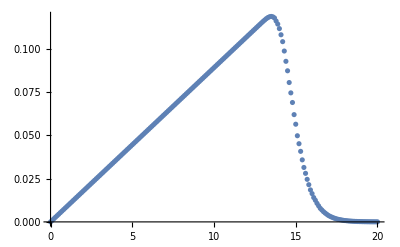

```mathematica
ListPlot[dσdbls]
```

Compare to MC Glauber :

```mathematica
Import["impactpar.pdf"]
```

Import::nffil: File not found during Import.

$Failed

The optical Glauber has a sharper edge.

So it does not do the trick.

```mathematica
dσdbInterp=Interpolation[dσdbls,InterpolationOrder->1]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
NIntegrate[dσdbInterp[b],{b,0,20}]
```

0.999564

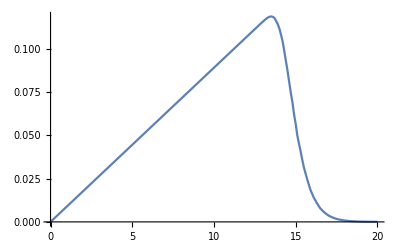

```mathematica
Plot[dσdbInterp[b],{b,0,20}]
```

```mathematica
cpInterp[b_]:= NIntegrate[dσdbInterp[bi] ,{bi,0,b}]
```

```mathematica
cpls=Table[{b,cpInterp[b]},{b,0,20,0.1}]
```

{{0.,0},{0.1,0.0000445204},{0.2,0.000178082},{0.3,0.000400684},{0.4,0.000712327},{0.5,0.00111301},{0.6,0.00160274},{0.7,0.0021815},{0.8,0.00284931},{0.9,0.00360616},{1.,0.00445204},{1.1,0.00538697},{1.2,0.00641094},{1.3,0.00752396},{1.4,0.00872601},{1.5,0.0100171},{1.6,0.0113972},{1.7,0.0128664},{1.8,0.0144246},{1.9,0.0160719},{2.,0.0178082},{2.1,0.0196335},{2.2,0.0215479},{2.3,0.0235513},{2.4,0.0256438},{2.5,0.0278253},{2.6,0.0300958},{2.7,0.0324554},{2.8,0.034904},{2.9,0.0374417},{3.,0.0400684},{3.1,0.0427841},{3.2,0.0455889},{3.3,0.0484828},{3.4,0.0514656},{3.5,0.0545375},{3.6,0.0576985},{3.7,0.0609485},{3.8,0.0642875},{3.9,0.0677156},{4.,0.0712327},{4.1,0.0748389},{4.2,0.0785341},{4.3,0.0823183},{4.4,0.0861916},{4.5,0.0901539},{4.6,0.0942053},{4.7,0.0983457},{4.8,0.102575},{4.9,0.106894},{5.,0.111301},{5.1,0.115798},{5.2,0.120383},{5.3,0.125058},{5.4,0.129822},{5.5,0.134674},{5.6,0.139616},{5.7,0.144647},{5.8,0.149767},{5.9,0.154976},{6.,0.160274},{6.1,0.165661},{6.2,0.171137},{6.3,0.176702},{6.4,0.182356},{6.5,0.188099},{6.6,0.193931},{6.7,0.199852},{6.8,0.205863},{6.9,0.211962},{7.,0.21815},{7.1,0.224428},{7.2,0.230794},{7.3,0.237249},{7.4,0.243794},{7.5,0.250428},{7.6,0.25715},{7.7,0.263962},{7.8,0.270862},{7.9,0.277852},{8.,0.284931},{8.1,0.292099},{8.2,0.299355},{8.3,0.306701},{8.4,0.314136},{8.5,0.32166},{8.6,0.329273},{8.7,0.336975},{8.8,0.344766},{8.9,0.352646},{9.,0.360616},{9.1,0.368674},{9.2,0.376821},{9.3,0.385057},{9.4,0.393383},{9.5,0.401797},{9.6,0.4103},{9.7,0.418893},{9.8,0.427574},{9.9,0.436345},{10.,0.445204},{10.1,0.454153},{10.2,0.463191},{10.3,0.472317},{10.4,0.481533},{10.5,0.490838},{10.6,0.500232},{10.7,0.509715},{10.8,0.519286},{10.9,0.528947},{11.,0.538697},{11.1,0.548536},{11.2,0.558464},{11.3,0.568482},{11.4,0.578588},{11.5,0.588783},{11.6,0.599067},{11.7,0.60944},{11.8,0.619903},{11.9,0.630454},{12.,0.641094},{12.1,0.651824},{12.2,0.662642},{12.3,0.67355},{12.4,0.684546},{12.5,0.695632},{12.6,0.706807},{12.7,0.71807},{12.8,0.729422},{12.9,0.740863},{13.,0.752391},{13.1,0.764004},{13.2,0.775697},{13.3,0.787463},{13.4,0.799284},{13.5,0.811136},{13.6,0.822985},{13.7,0.834792},{13.8,0.846479},{13.9,0.857988},{14.,0.869277},{14.1,0.880258},{14.2,0.890863},{14.3,0.900998},{14.4,0.910566},{14.5,0.919563},{14.6,0.927947},{14.7,0.935695},{14.8,0.942866},{14.9,0.949409},{15.,0.955325},{15.1,0.960632},{15.2,0.965376},{15.3,0.969669},{15.4,0.973496},{15.5,0.976858},{15.6,0.979831},{15.7,0.982461},{15.8,0.984764},{15.9,0.986761},{16.,0.988501},{16.1,0.99002},{16.2,0.991347},{16.3,0.992507},{16.4,0.993506},{16.5,0.994361},{16.6,0.995096},{16.7,0.995734},{16.8,0.996284},{16.9,0.996759},{17.,0.997165},{17.1,0.997511},{17.2,0.997809},{17.3,0.998067},{17.4,0.998287},{17.5,0.998476},{17.6,0.998636},{17.7,0.998774},{17.8,0.998894},{17.9,0.998996},{18.,0.999082},{18.1,0.999156},{18.2,0.999219},{18.3,0.999273},{18.4,0.999319},{18.5,0.999359},{18.6,0.999392},{18.7,0.999421},{18.8,0.999445},{18.9,0.999466},{19.,0.999484},{19.1,0.999498},{19.2,0.999511},{19.3,0.999522},{19.4,0.999531},{19.5,0.999539},{19.6,0.999546},{19.7,0.999552},{19.8,0.999556},{19.9,0.999561},{20.,0.999564}}

```mathematica
cInterp=Interpolation[cpls]
```

InterpolatingFunction[{{0., 20.}}, <>]

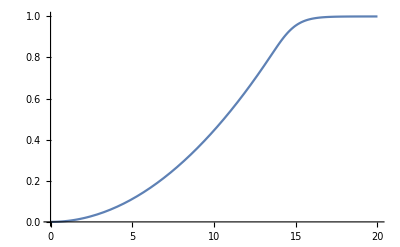

```mathematica
Plot[cInterp[b],{b,0,20}]
```

### b for centrality bins

Refined b list :

```mathematica
bls=Table[{cbin,c/.FindRoot[cInterp[c]==cbin,{c,1.0}]},{cbin,0.01,0.05,0.01}]
```

{{0.01,1.54705},{0.02,2.18786},{0.03,2.67957},{0.04,3.0941},{0.05,3.45931}}

```mathematica
bls=Join[bls,Table[{cbin,c/.FindRoot[cInterp[c]==cbin,{c,10*cbin}]},{cbin,0.1,0.95,0.05}]]
```

{{0.01,1.54705},{0.02,2.18786},{0.03,2.67957},{0.04,3.0941},{0.05,3.45931},{0.1,4.8922},{0.15,5.9917},{0.2,6.91862},{0.25,7.73525},{0.3,8.47355},{0.35,9.15248},{0.4,9.78441},{0.45,10.3779},{0.5,10.9393},{0.55,11.4732},{0.6,11.9834},{0.65,12.4727},{0.7,12.9436},{0.75,13.3979},{0.8,13.8377},{0.85,14.2701},{0.9,14.7299},{0.95,15.3213}}

```mathematica
bls=Join[{{0,0}},bls,{{1.0,20}}]
```

{{0,0},{0.01,1.54705},{0.02,2.18786},{0.03,2.67957},{0.04,3.0941},{0.05,3.45931},{0.1,4.8922},{0.15,5.9917},{0.2,6.91862},{0.25,7.73525},{0.3,8.47355},{0.35,9.15248},{0.4,9.78441},{0.45,10.3779},{0.5,10.9393},{0.55,11.4732},{0.6,11.9834},{0.65,12.4727},{0.7,12.9436},{0.75,13.3979},{0.8,13.8377},{0.85,14.2701},{0.9,14.7299},{0.95,15.3213},{1.,20}}

Coarse b list :

```mathematica
cls={0.05,0.1,0.2,0.4,0.6,0.8};
bcls=Table[{cls[[i]],c/.FindRoot[cInterp[c]==cls[[i]],{c,10*cls[[i]]}]},{i,1,Length[cls]}]
```

{{0.05,3.45931},{0.1,4.8922},{0.2,6.91862},{0.4,9.78441},{0.6,11.9834},{0.8,13.8377}}

```mathematica
bcls=Join[{{0,0}},bcls,{{1.0,20}}]
```

{{0,0},{0.05,3.45931},{0.1,4.8922},{0.2,6.91862},{0.4,9.78441},{0.6,11.9834},{0.8,13.8377},{1.,20}}

They agree with Table I very well.

```mathematica
cls={0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85};
bcls=Table[{cls[[i]],c/.FindRoot[cInterp[c]==cls[[i]],{c,10*cls[[i]]}]},{i,1,Length[cls]}]
```

{{0.05,3.45931},{0.15,5.9917},{0.25,7.73525},{0.35,9.15248},{0.45,10.3779},{0.55,11.4732},{0.65,12.4727},{0.75,13.3979},{0.85,14.2704}}

```mathematica
bcls=Join[{{0,0}},bcls,{{1.0,20}}]
```

{{0,0},{0.05,3.45931},{0.15,5.9917},{0.25,7.73525},{0.35,9.15248},{0.45,10.3779},{0.55,11.4732},{0.65,12.4727},{0.75,13.3979},{0.85,14.2704},{1.,20}}

## Flow

We take the initial energy density to be proportional to ρws[x,y-b/2] ρws[x,y+b/2].

Recall that the Thickness function in 1/fm^2 :

```mathematica
TAB[b_?NumericQ]:=NIntegrate[ρws[sx,sy-b/2,zA]*ρws[sx,sy+b/2,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo"(*,Method->{"MonteCarloRule","Points"->10^4}*)}]
```

```mathematica
Rrms[b_?NumericQ]:=Sqrt[1/TAB[b] NIntegrate[(sx^2+sy^2)ρws[sx,sy-b/2,zA]*ρws[sx,sy+b/2,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo"(*,Method->{"MonteCarloRule","Points"->10^6}*)}]]
```

```mathematica
δ2[b_?NumericQ]:=NIntegrate[(sx^2-sy^2)ρws[sx,sy-b/2,zA]*ρws[sx,sy+b/2,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->10^6}}]/NIntegrate[(sx^2+sy^2)ρws[sx,sy-b/2,zA]*ρws[sx,sy+b/2,zB],{sx,-Infinity,Infinity},{sy,-Infinity,Infinity},{zA,-Infinity,Infinity},{zB,-Infinity,Infinity},Method->{"AdaptiveMonteCarlo"(*,Method->{"MonteCarloRule","Points"->10^6}*)}]
```

```mathematica
cls=Table[0.005*n,{n,0,180}]
```

{0.,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105,0.11,0.115,0.12,0.125,0.13,0.135,0.14,0.145,0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6,0.605,0.61,0.615,0.62,0.625,0.63,0.635,0.64,0.645,0.65,0.655,0.66,0.665,0.67,0.675,0.68,0.685,0.69,0.695,0.7,0.705,0.71,0.715,0.72,0.725,0.73,0.735,0.74,0.745,0.75,0.755,0.76,0.765,0.77,0.775,0.78,0.785,0.79,0.795,0.8,0.805,0.81,0.815,0.82,0.825,0.83,0.835,0.84,0.845,0.85,0.855,0.86,0.865,0.87,0.875,0.88,0.885,0.89,0.895,0.9}

```mathematica
(* cls={0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.52,0.54,0.56,0.58,0.60,0.64,0.655,0.685,0.715,0.735,0.765,0.79,0.815,0.845,0.9,0.94,0.98};*)
bcls=Table[{cls[[i]],c/.FindRoot[cInterp[c]==cls[[i]],{c,10*cls[[i]]}]},{i,1,Length[cls]}]
```

{{0.,0.},{0.005,1.05975},{0.01,1.49872},{0.015,1.83555},{0.02,2.11951},{0.025,2.36968},{0.03,2.59586},{0.035,2.80385},{0.04,2.99744},{0.045,3.17926},{0.05,3.35124},{0.055,3.51481},{0.06,3.6711},{0.065,3.821},{0.07,3.96524},{0.075,4.10441},{0.08,4.23902},{0.085,4.36948},{0.09,4.49616},{0.095,4.61936},{0.1,4.73937},{0.105,4.85641},{0.11,4.97069},{0.115,5.0824},{0.12,5.19172},{0.125,5.29877},{0.13,5.40371},{0.135,5.50665},{0.14,5.60769},{0.145,5.70695},{0.15,5.80451},{0.155,5.90046},{0.16,5.99488},{0.165,6.08783},{0.17,6.17938},{0.175,6.26959},{0.18,6.35853},{0.185,6.44623},{0.19,6.53277},{0.195,6.61816},{0.2,6.70248},{0.205,6.78574},{0.21,6.86799},{0.215,6.94927},{0.22,7.02962},{0.225,7.10905},{0.23,7.1876},{0.235,7.26531},{0.24,7.34219},{0.245,7.41828},{0.25,7.4936},{0.255,7.56816},{0.26,7.642},{0.265,7.71513},{0.27,7.78757},{0.275,7.85935},{0.28,7.93048},{0.285,8.00097},{0.29,8.07085},{0.295,8.14013},{0.3,8.20882},{0.305,8.27695},{0.31,8.34451},{0.315,8.41154},{0.32,8.47804},{0.325,8.54401},{0.33,8.60949},{0.335,8.67446},{0.34,8.73896},{0.345,8.80298},{0.35,8.86654},{0.355,8.92965},{0.36,8.99231},{0.365,9.05455},{0.37,9.11635},{0.375,9.17774},{0.38,9.23873},{0.385,9.29931},{0.39,9.3595},{0.395,9.4193},{0.4,9.47873},{0.405,9.53779},{0.41,9.59648},{0.415,9.65482},{0.42,9.71281},{0.425,9.77045},{0.43,9.82776},{0.435,9.88473},{0.44,9.94138},{0.445,9.9977},{0.45,10.0537},{0.455,10.1094},{0.46,10.1648},{0.465,10.2199},{0.47,10.2747},{0.475,10.3292},{0.48,10.3834},{0.485,10.4374},{0.49,10.491},{0.495,10.5444},{0.5,10.5975},{0.505,10.6504},{0.51,10.703},{0.515,10.7553},{0.52,10.8074},{0.525,10.8593},{0.53,10.9108},{0.535,10.9622},{0.54,11.0133},{0.545,11.0642},{0.55,11.1148},{0.555,11.1652},{0.56,11.2154},{0.565,11.2653},{0.57,11.3151},{0.575,11.3646},{0.58,11.4139},{0.585,11.463},{0.59,11.5119},{0.595,11.5606},{0.6,11.609},{0.605,11.6573},{0.61,11.7054},{0.615,11.7532},{0.62,11.8009},{0.625,11.8484},{0.63,11.8957},{0.635,11.9428},{0.64,11.9898},{0.645,12.0365},{0.65,12.0831},{0.655,12.1294},{0.66,12.1757},{0.665,12.2217},{0.67,12.2675},{0.675,12.3132},{0.68,12.3588},{0.685,12.4041},{0.69,12.4493},{0.695,12.4943},{0.7,12.5392},{0.705,12.5839},{0.71,12.6284},{0.715,12.6728},{0.72,12.7171},{0.725,12.7611},{0.73,12.8051},{0.735,12.8488},{0.74,12.8925},{0.745,12.936},{0.75,12.9793},{0.755,13.0225},{0.76,13.0656},{0.765,13.1085},{0.77,13.1514},{0.775,13.1941},{0.78,13.2366},{0.785,13.2791},{0.79,13.3215},{0.795,13.3638},{0.8,13.406},{0.805,13.4482},{0.81,13.4904},{0.815,13.5326},{0.82,13.5748},{0.825,13.617},{0.83,13.6593},{0.835,13.7018},{0.84,13.7444},{0.845,13.7873},{0.85,13.8304},{0.855,13.8739},{0.86,13.9177},{0.865,13.9618},{0.87,14.0065},{0.875,14.0517},{0.88,14.0976},{0.885,14.1442},{0.89,14.1917},{0.895,14.2402},{0.9,14.2899}}

```mathematica
bcls=Join[bcls,{{1.0,20}}]
```

{{0.,0.},{0.005,1.05975},{0.01,1.49872},{0.015,1.83555},{0.02,2.11951},{0.025,2.36968},{0.03,2.59586},{0.035,2.80385},{0.04,2.99744},{0.045,3.17926},{0.05,3.35124},{0.055,3.51481},{0.06,3.6711},{0.065,3.821},{0.07,3.96524},{0.075,4.10441},{0.08,4.23902},{0.085,4.36948},{0.09,4.49616},{0.095,4.61936},{0.1,4.73937},{0.105,4.85641},{0.11,4.97069},{0.115,5.0824},{0.12,5.19172},{0.125,5.29877},{0.13,5.40371},{0.135,5.50665},{0.14,5.60769},{0.145,5.70695},{0.15,5.80451},{0.155,5.90046},{0.16,5.99488},{0.165,6.08783},{0.17,6.17938},{0.175,6.26959},{0.18,6.35853},{0.185,6.44623},{0.19,6.53277},{0.195,6.61816},{0.2,6.70248},{0.205,6.78574},{0.21,6.86799},{0.215,6.94927},{0.22,7.02962},{0.225,7.10905},{0.23,7.1876},{0.235,7.26531},{0.24,7.34219},{0.245,7.41828},{0.25,7.4936},{0.255,7.56816},{0.26,7.642},{0.265,7.71513},{0.27,7.78757},{0.275,7.85935},{0.28,7.93048},{0.285,8.00097},{0.29,8.07085},{0.295,8.14013},{0.3,8.20882},{0.305,8.27695},{0.31,8.34451},{0.315,8.41154},{0.32,8.47804},{0.325,8.54401},{0.33,8.60949},{0.335,8.67446},{0.34,8.73896},{0.345,8.80298},{0.35,8.86654},{0.355,8.92965},{0.36,8.99231},{0.365,9.05455},{0.37,9.11635},{0.375,9.17774},{0.38,9.23873},{0.385,9.29931},{0.39,9.3595},{0.395,9.4193},{0.4,9.47873},{0.405,9.53779},{0.41,9.59648},{0.415,9.65482},{0.42,9.71281},{0.425,9.77045},{0.43,9.82776},{0.435,9.88473},{0.44,9.94138},{0.445,9.9977},{0.45,10.0537},{0.455,10.1094},{0.46,10.1648},{0.465,10.2199},{0.47,10.2747},{0.475,10.3292},{0.48,10.3834},{0.485,10.4374},{0.49,10.491},{0.495,10.5444},{0.5,10.5975},{0.505,10.6504},{0.51,10.703},{0.515,10.7553},{0.52,10.8074},{0.525,10.8593},{0.53,10.9108},{0.535,10.9622},{0.54,11.0133},{0.545,11.0642},{0.55,11.1148},{0.555,11.1652},{0.56,11.2154},{0.565,11.2653},{0.57,11.3151},{0.575,11.3646},{0.58,11.4139},{0.585,11.463},{0.59,11.5119},{0.595,11.5606},{0.6,11.609},{0.605,11.6573},{0.61,11.7054},{0.615,11.7532},{0.62,11.8009},{0.625,11.8484},{0.63,11.8957},{0.635,11.9428},{0.64,11.9898},{0.645,12.0365},{0.65,12.0831},{0.655,12.1294},{0.66,12.1757},{0.665,12.2217},{0.67,12.2675},{0.675,12.3132},{0.68,12.3588},{0.685,12.4041},{0.69,12.4493},{0.695,12.4943},{0.7,12.5392},{0.705,12.5839},{0.71,12.6284},{0.715,12.6728},{0.72,12.7171},{0.725,12.7611},{0.73,12.8051},{0.735,12.8488},{0.74,12.8925},{0.745,12.936},{0.75,12.9793},{0.755,13.0225},{0.76,13.0656},{0.765,13.1085},{0.77,13.1514},{0.775,13.1941},{0.78,13.2366},{0.785,13.2791},{0.79,13.3215},{0.795,13.3638},{0.8,13.406},{0.805,13.4482},{0.81,13.4904},{0.815,13.5326},{0.82,13.5748},{0.825,13.617},{0.83,13.6593},{0.835,13.7018},{0.84,13.7444},{0.845,13.7873},{0.85,13.8304},{0.855,13.8739},{0.86,13.9177},{0.865,13.9618},{0.87,14.0065},{0.875,14.0517},{0.88,14.0976},{0.885,14.1442},{0.89,14.1917},{0.895,14.2402},{0.9,14.2899},{1.,20}}

```mathematica
δ2ls=Table[{0.5*(bcls[[i,1]]+bcls[[i+1,1]]),δ2[0.5*(bcls[[i,2]]+bcls[[i+1,2]])]},{i,1,Length[bcls]-2}]
```

NIntegrate::maxp: The integral failed to converge after 3000000 integrand evaluations. NIntegrate obtained 0.000517805 and 0.000128631 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 3000000 integrand evaluations. NIntegrate obtained 0.00165697 and 0.000121441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 3000000 integrand evaluations. NIntegrate obtained 0.00279232 and 0.000116161 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

$Aborted

```mathematica
Show[-Graphics-,ListPlot[Transpose[{0.5*(bcls[[1;;-3,2]]+bcls[[2;;-2,2]]),δ2ls[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
ListPlot[δ2ls,AxesLabel->{"Centrality", "δ_2"}]
```

-Graphics-

```mathematica
Show[-Graphics-,Plot[0.1+0.4*x,{x,0,0.1}]]
```

-Graphics-

```mathematica
Rls=Table[{0.5*(bcls[[i,1]]+bcls[[i+1,1]]),Rrms[0.5*(bcls[[i,2]]+bcls[[i+1,2]])]},{i,1,Length[bcls]-2}]
```

{{0.0025,3.6408},{0.0075,3.62913},{0.0125,3.54284},{0.0175,3.60847},{0.0225,3.57467},{0.0275,3.48728},{0.0325,3.51636},{0.0375,3.46247},{0.0425,3.47855},{0.0475,3.44682},{0.0525,3.35867},{0.0575,3.38367},{0.0625,3.38632},{0.0675,3.37515},{0.0725,3.28506},{0.0775,3.27063},{0.0825,3.24976},{0.0875,3.25},{0.0925,3.24641},{0.0975,3.21421},{0.1025,3.17429},{0.1075,3.12442},{0.1125,3.09209},{0.1175,3.10495},{0.1225,3.09429},{0.1275,3.08022},{0.1325,3.07308},{0.1375,3.06349},{0.1425,3.02811},{0.1475,3.01778},{0.1525,2.97153},{0.1575,2.98821},{0.1625,2.98284},{0.1675,2.95249},{0.1725,2.93194},{0.1775,2.93203},{0.1825,2.86502},{0.1875,2.88168},{0.1925,2.90052},{0.1975,2.88621},{0.2025,2.87283},{0.2075,2.79989},{0.2125,2.84744},{0.2175,2.81383},{0.2225,2.7987},{0.2275,2.79325},{0.2325,2.74165},{0.2375,2.75977},{0.2425,2.72425},{0.2475,2.70505},{0.2525,2.6973},{0.2575,2.69842},{0.2625,2.6932},{0.2675,2.66297},{0.2725,2.61965},{0.2775,2.63765},{0.2825,2.61271},{0.2875,2.61567},{0.2925,2.57162},{0.2975,2.55126},{0.3025,2.5689},{0.3075,2.54133},{0.3125,2.56621},{0.3175,2.55652},{0.3225,2.54427},{0.3275,2.52973},{0.3325,2.49356},{0.3375,2.47843},{0.3425,2.50979},{0.3475,2.49234},{0.3525,2.46368},{0.3575,2.44551},{0.3625,2.44683},{0.3675,2.42627},{0.3725,2.38651},{0.3775,2.4321},{0.3825,2.38594},{0.3875,2.39726},{0.3925,2.37139},{0.3975,2.38865},{0.4025,2.36428},{0.4075,2.333},{0.4125,2.3174},{0.4175,2.3372},{0.4225,2.33602},{0.4275,2.30125},{0.4325,2.30246},{0.4375,2.29654},{0.4425,2.29387},{0.4475,2.32063},{0.4525,2.2793},{0.4575,2.26746},{0.4625,2.24579},{0.4675,2.20839},{0.4725,2.25158},{0.4775,2.2199},{0.4825,2.21691},{0.4875,2.18848},{0.4925,2.2242},{0.4975,2.17684},{0.5025,2.16895},{0.5075,2.21157},{0.5125,2.20287},{0.5175,2.15569},{0.5225,2.18418},{0.5275,2.17135},{0.5325,2.15129},{0.5375,2.1574},{0.5425,2.15147},{0.5475,2.14047},{0.5525,2.10917},{0.5575,2.11877},{0.5625,2.09802},{0.5675,2.08076},{0.5725,2.09826},{0.5775,2.11436},{0.5825,2.11625},{0.5875,2.08494},{0.5925,2.08706},{0.5975,2.0676},{0.6025,2.07429},{0.6075,2.05777},{0.6125,2.07023},{0.6175,2.03854},{0.6225,2.05336},{0.6275,2.0597},{0.6325,2.0776},{0.6375,2.0388},{0.6425,2.04676},{0.6475,2.06431},{0.6525,2.06832},{0.6575,2.01605},{0.6625,2.02306},{0.6675,2.05049},{0.6725,2.04476},{0.6775,2.01479},{0.6825,2.01747},{0.6875,2.00981},{0.6925,2.04492},{0.6975,2.011},{0.7025,1.99783},{0.7075,2.00339},{0.7125,1.99089},{0.7175,1.99148},{0.7225,2.01534},{0.7275,2.00661},{0.7325,1.96057},{0.7375,1.98436},{0.7425,1.99037},{0.7475,2.01623},{0.7525,2.03169},{0.7575,2.00034},{0.7625,2.04433},{0.7675,2.00036},{0.7725,2.00198},{0.7775,2.02572},{0.7825,1.99914},{0.7875,2.00175},{0.7925,1.9782},{0.7975,2.01339},{0.8025,2.02129},{0.8075,1.99654},{0.8125,2.02584},{0.8175,1.993},{0.8225,2.05259},{0.8275,2.00993},{0.8325,2.03645},{0.8375,2.03256},{0.8425,2.01633},{0.8475,2.02759},{0.8525,2.02714},{0.8575,2.03929},{0.8625,2.04223},{0.8675,2.04609},{0.8725,2.01688},{0.8775,2.08649},{0.8825,2.06607},{0.8875,2.07818},{0.8925,2.06106}}